```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
```

/Users/zack/Documents/ignition/cantera/ratematrix

## Random matrices

data/random2

{996,5,0.00682633}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

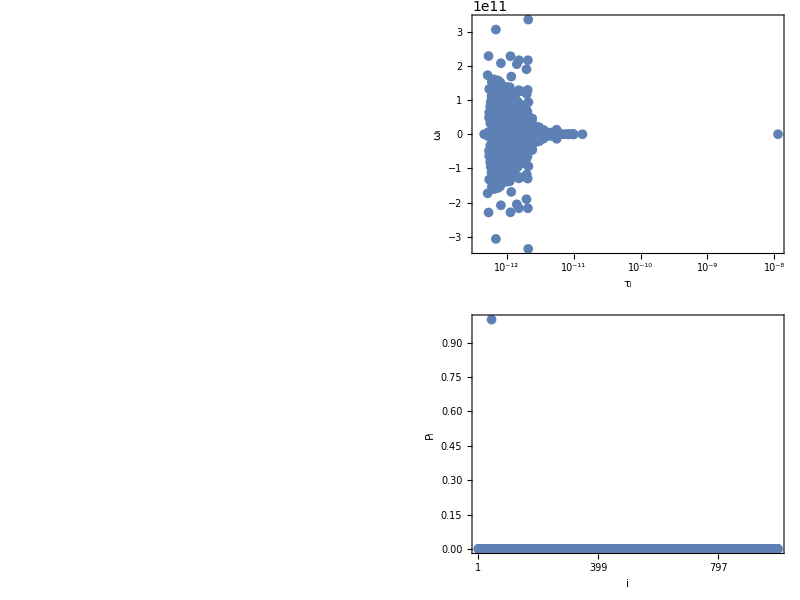

```mathematica
filebase="data/random2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
A=SparseArray[Table[{columns[[i]]+1,rows[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Transition matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}},MaxPlotPoints->200]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
```

data/random2

{996,5,0.00682633}

28.459

{12.3703,Null}

8.62557×10^11

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

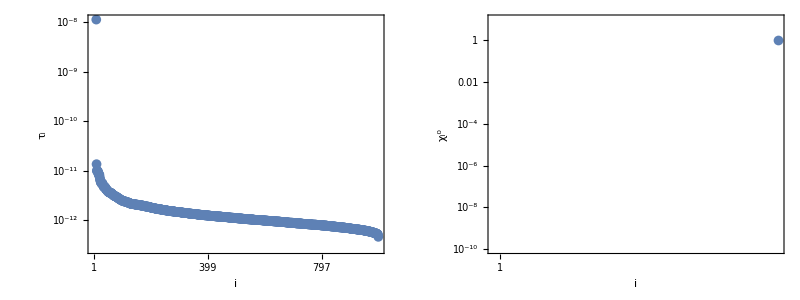

fig3.pdf

0.880026

```mathematica
filebase="data/random2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
r=1/2;
AbsoluteTiming[angles=ParallelTable[ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}];]
max=Pi/2;
r=1;
cf=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*(Pi/2-#)/max]&;
max2=N[Max[A]]
cf2=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*#/max2]&;
p=Grid[{{Show[rasterizeBackground[MatrixPlot[Abs[A],ImageSize->350,AspectRatio->r,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[{Round[i],""},{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{None,None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},MaxPlotPoints->200]],Epilog->Inset[BarLegend[{cf2,{0,max2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->DisplayForm[RowBox[{Subsuperscript[W,i,k],"/",HoldForm[10^18]}]]],ImageScaled[{0.55,0.88}]]],Show[rasterizeBackground[MatrixPlot[angles,ImageSize->350,AspectRatio->r,PlotRange->All,FrameTicks->{Table[Round[i],{i,1,Length[evecs],(Length[evecs]-1)/5}],Table[{Round[i],""},{i,1,Length[evecs],(Length[evecs]-1)/5}]},FrameLabel->{{None,
None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},ColorFunctionScaling->False,ColorFunction->cf]],Epilog->Inset[BarLegend[{cf,{Pi/2-max,Pi/2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->Subsuperscript[θ,i,k]],ImageScaled[{0.55,0.88}]]]},{ListLogPlot[Reverse[-1/Re[evals[[1;;-2]]]],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript[τ,i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImagePadding->{{80,25},{65,10}},ImageSize->350,FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],ListLogPlot[Abs[evecs[[-1]]],PlotRange->{10^-10,10},Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subsuperscript[χ,i,0]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]]}}]
Export["fig3.pdf",p]
Total[Abs[evals]^2]/Total[svals^2]
```

```mathematica
Count[Eigenvalues[A+Transpose[A]],u_/;Re[u]>=0]
Count[Eigenvalues[A],u_/;Re[u]>=0]
```

Eigenvalues::arh: Because finding 996 out of the 996 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

11

Eigenvalues::arh: Because finding 996 out of the 996 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

9

```mathematica
evals
```

{-2.18574×10^12+0. ⅈ,-2.01434×10^12+0. ⅈ,-1.93673×10^12-1.72848×10^11 ⅈ,-1.93673×10^12+1.72848×10^11 ⅈ,-1.90505×10^12-5.8051×10^9 ⅈ,-1.90505×10^12+5.8051×10^9 ⅈ,-1.8758×10^12-2.28982×10^11 ⅈ,-1.8758×10^12+2.28982×10^11 ⅈ,-1.85634×10^12-3.83419×10^9 ⅈ,-1.85634×10^12+3.83419×10^9 ⅈ,-1.85058×10^12-4.84938×10^10 ⅈ,-1.85058×10^12+4.84938×10^10 ⅈ,-1.83499×10^12-1.3254×10^11 ⅈ,-1.83499×10^12+1.3254×10^11 ⅈ,-1.83399×10^12-6.35247×10^10 ⅈ,-1.83399×10^12+6.35247×10^10 ⅈ,-1.80827×10^12+0. ⅈ,-1.79234×10^12+0. ⅈ,-1.773×10^12-8.0743×10^10 ⅈ,-1.773×10^12+8.0743×10^10 ⅈ,-1.76809×10^12-3.24726×10^10 ⅈ,-1.76809×10^12+3.24726×10^10 ⅈ,-1.75297×10^12+0. ⅈ,-1.75055×10^12-6.31711×10^10 ⅈ,-1.75055×10^12+6.31711×10^10 ⅈ,-1.74216×10^12-9.50079×10^10 ⅈ,-1.74216×10^12+9.50079×10^10 ⅈ,-1.72836×10^12+0. ⅈ,-1.71947×10^12-7.32391×10^10 ⅈ,-1.71947×10^12+7.32391×10^10 ⅈ,-1.69804×10^12-5.32606×10^10 ⅈ,-1.69804×10^12+5.32606×10^10 ⅈ,-1.69579×10^12-4.04818×10^10 ⅈ,-1.69579×10^12+4.04818×10^10 ⅈ,-1.69575×10^12-1.11699×10^11 ⅈ,-1.69575×10^12+1.11699×10^11 ⅈ,-1.67659×10^12-1.53134×10^11 ⅈ,-1.67659×10^12+1.53134×10^11 ⅈ,-1.65991×10^12-5.81673×10^10 ⅈ,-1.65991×10^12+5.81673×10^10 ⅈ,-1.65372×10^12-1.09648×10^10 ⅈ,-1.65372×10^12+1.09648×10^10 ⅈ,-1.64828×10^12-9.55813×10^10 ⅈ,-1.64828×10^12+9.55813×10^10 ⅈ,-1.64089×10^12-3.14236×10^10 ⅈ,-1.64089×10^12+3.14236×10^10 ⅈ,-1.63556×10^12-1.29083×10^11 ⅈ,-1.63556×10^12+1.29083×10^11 ⅈ,-1.63478×10^12-1.02594×10^11 ⅈ,-1.63478×10^12+1.02594×10^11 ⅈ,-1.61655×10^12-7.49401×10^10 ⅈ,-1.61655×10^12+7.49401×10^10 ⅈ,-1.61417×10^12+0. ⅈ,-1.60489×10^12-1.50388×10^11 ⅈ,-1.60489×10^12+1.50388×10^11 ⅈ,-1.59945×10^12+0. ⅈ,-1.59793×10^12-6.69264×10^10 ⅈ,-1.59793×10^12+6.69264×10^10 ⅈ,-1.59791×10^12-3.05633×10^10 ⅈ,-1.59791×10^12+3.05633×10^10 ⅈ,-1.59016×10^12-2.68997×10^10 ⅈ,-1.59016×10^12+2.68997×10^10 ⅈ,-1.58941×10^12-4.97014×10^10 ⅈ,-1.58941×10^12+4.97014×10^10 ⅈ,-1.58021×10^12+0. ⅈ,-1.5642×10^12-7.46264×10^10 ⅈ,-1.5642×10^12+7.46264×10^10 ⅈ,-1.55834×10^12-1.18592×10^11 ⅈ,-1.55834×10^12+1.18592×10^11 ⅈ,-1.55716×10^12+0. ⅈ,-1.55604×10^12-1.60664×10^11 ⅈ,-1.55604×10^12+1.60664×10^11 ⅈ,-1.55129×10^12-3.19512×10^10 ⅈ,-1.55129×10^12+3.19512×10^10 ⅈ,-1.5434×10^12+0. ⅈ,-1.54195×10^12-3.13814×10^10 ⅈ,-1.54195×10^12+3.13814×10^10 ⅈ,-1.5403×10^12+0. ⅈ,-1.53638×10^12-1.00782×10^11 ⅈ,-1.53638×10^12+1.00782×10^11 ⅈ,-1.52117×10^12-4.13133×10^10 ⅈ,-1.52117×10^12+4.13133×10^10 ⅈ,-1.51463×10^12+0. ⅈ,-1.51387×10^12-1.19521×10^11 ⅈ,-1.51387×10^12+1.19521×10^11 ⅈ,-1.51314×10^12-1.0098×10^11 ⅈ,-1.51314×10^12+1.0098×10^11 ⅈ,-1.5122×10^12-1.43748×10^10 ⅈ,-1.5122×10^12+1.43748×10^10 ⅈ,-1.50603×10^12-7.86598×10^10 ⅈ,-1.50603×10^12+7.86598×10^10 ⅈ,-1.49679×10^12-1.38447×10^11 ⅈ,-1.49679×10^12+1.38447×10^11 ⅈ,-1.49676×10^12+0. ⅈ,-1.4906×10^12-4.81467×10^10 ⅈ,-1.4906×10^12+4.81467×10^10 ⅈ,-1.48945×10^12-2.09258×10^10 ⅈ,-1.48945×10^12+2.09258×10^10 ⅈ,-1.48103×10^12-7.46917×10^10 ⅈ,-1.48103×10^12+7.46917×10^10 ⅈ,-1.47186×10^12-4.70661×10^10 ⅈ,-1.47186×10^12+4.70661×10^10 ⅈ,-1.46343×10^12-3.0324×10^9 ⅈ,-1.46343×10^12+3.0324×10^9 ⅈ,-1.46094×10^12-8.59607×10^10 ⅈ,-1.46094×10^12+8.59607×10^10 ⅈ,-1.45949×10^12-2.54172×10^10 ⅈ,-1.45949×10^12+2.54172×10^10 ⅈ,-1.45897×10^12-3.06417×10^11 ⅈ,-1.45897×10^12+3.06417×10^11 ⅈ,-1.44684×10^12-1.83683×10^10 ⅈ,-1.44684×10^12+1.83683×10^10 ⅈ,-1.44528×10^12-8.51825×10^10 ⅈ,-1.44528×10^12+8.51825×10^10 ⅈ,-1.44279×10^12+0. ⅈ,-1.43457×10^12-1.39365×10^11 ⅈ,-1.43457×10^12+1.39365×10^11 ⅈ,-1.4228×10^12-2.79025×10^10 ⅈ,-1.4228×10^12+2.79025×10^10 ⅈ,-1.4217×10^12-1.05346×10^11 ⅈ,-1.4217×10^12+1.05346×10^11 ⅈ,-1.42014×10^12-4.54209×10^10 ⅈ,-1.42014×10^12+4.54209×10^10 ⅈ,-1.41873×10^12+0. ⅈ,-1.41787×10^12+0. ⅈ,-1.41341×10^12-7.65857×10^10 ⅈ,-1.41341×10^12+7.65857×10^10 ⅈ,-1.4113×10^12-1.29093×10^11 ⅈ,-1.4113×10^12+1.29093×10^11 ⅈ,-1.40543×10^12-3.79107×10^10 ⅈ,-1.40543×10^12+3.79107×10^10 ⅈ,-1.40349×10^12-2.05416×10^10 ⅈ,-1.40349×10^12+2.05416×10^10 ⅈ,-1.40081×10^12-7.47549×10^10 ⅈ,-1.40081×10^12+7.47549×10^10 ⅈ,-1.39894×10^12-3.96267×10^9 ⅈ,-1.39894×10^12+3.96267×10^9 ⅈ,-1.39863×10^12-1.02592×10^11 ⅈ,-1.39863×10^12+1.02592×10^11 ⅈ,-1.39054×10^12-1.51733×10^10 ⅈ,-1.39054×10^12+1.51733×10^10 ⅈ,-1.37832×10^12-5.8054×10^10 ⅈ,-1.37832×10^12+5.8054×10^10 ⅈ,-1.37527×10^12-3.87162×10^10 ⅈ,-1.37527×10^12+3.87162×10^10 ⅈ,-1.37461×10^12+0. ⅈ,-1.36961×10^12-2.48434×10^10 ⅈ,-1.36961×10^12+2.48434×10^10 ⅈ,-1.3634×10^12-1.49436×10^10 ⅈ,-1.3634×10^12+1.49436×10^10 ⅈ,-1.36252×10^12-1.57528×10^11 ⅈ,-1.36252×10^12+1.57528×10^11 ⅈ,-1.3571×10^12-1.31459×10^11 ⅈ,-1.3571×10^12+1.31459×10^11 ⅈ,-1.35322×10^12-8.73955×10^10 ⅈ,-1.35322×10^12+8.73955×10^10 ⅈ,-1.35085×10^12+0. ⅈ,-1.34907×10^12-5.75762×10^10 ⅈ,-1.34907×10^12+5.75762×10^10 ⅈ,-1.34595×10^12-1.97185×10^10 ⅈ,-1.34595×10^12+1.97185×10^10 ⅈ,-1.34456×10^12-6.95896×10^10 ⅈ,-1.34456×10^12+6.95896×10^10 ⅈ,-1.34072×10^12-4.07935×10^10 ⅈ,-1.34072×10^12+4.07935×10^10 ⅈ,-1.33823×10^12-2.58392×10^10 ⅈ,-1.33823×10^12+2.58392×10^10 ⅈ,-1.3346×10^12-1.05896×10^11 ⅈ,-1.3346×10^12+1.05896×10^11 ⅈ,-1.33276×10^12+0. ⅈ,-1.32503×10^12+0. ⅈ,-1.32195×10^12-1.295×10^10 ⅈ,-1.32195×10^12+1.295×10^10 ⅈ,-1.31632×10^12-7.40231×10^10 ⅈ,-1.31632×10^12+7.40231×10^10 ⅈ,-1.31484×10^12-4.92583×10^10 ⅈ,-1.31484×10^12+4.92583×10^10 ⅈ,-1.31346×10^12+0. ⅈ,-1.30684×10^12+0. ⅈ,-1.30614×10^12-1.2457×10^11 ⅈ,-1.30614×10^12+1.2457×10^11 ⅈ,-1.29584×10^12-7.49475×10^10 ⅈ,-1.29584×10^12+7.49475×10^10 ⅈ,-1.29493×10^12-3.06623×10^10 ⅈ,-1.29493×10^12+3.06623×10^10 ⅈ,-1.29488×10^12-4.09393×10^10 ⅈ,-1.29488×10^12+4.09393×10^10 ⅈ,-1.29307×10^12-1.28142×10^11 ⅈ,-1.29307×10^12+1.28142×10^11 ⅈ,-1.29183×10^12-1.22013×10^10 ⅈ,-1.29183×10^12+1.22013×10^10 ⅈ,-1.29182×10^12+0. ⅈ,-1.28516×10^12-9.40808×10^10 ⅈ,-1.28516×10^12+9.40808×10^10 ⅈ,-1.28471×10^12+0. ⅈ,-1.28331×10^12+0. ⅈ,-1.28242×10^12-4.32727×10^10 ⅈ,-1.28242×10^12+4.32727×10^10 ⅈ,-1.27824×10^12-6.87116×10^10 ⅈ,-1.27824×10^12+6.87116×10^10 ⅈ,-1.27746×10^12-8.24131×10^10 ⅈ,-1.27746×10^12+8.24131×10^10 ⅈ,-1.27585×10^12-1.53354×10^11 ⅈ,-1.27585×10^12+1.53354×10^11 ⅈ,-1.26662×10^12-3.74082×10^10 ⅈ,-1.26662×10^12+3.74082×10^10 ⅈ,-1.26534×10^12+0. ⅈ,-1.26084×10^12-5.83752×10^10 ⅈ,-1.26084×10^12+5.83752×10^10 ⅈ,-1.26051×10^12+0. ⅈ,-1.26022×10^12-1.45293×10^10 ⅈ,-1.26022×10^12+1.45293×10^10 ⅈ,-1.25469×10^12-2.29854×10^10 ⅈ,-1.25469×10^12+2.29854×10^10 ⅈ,-1.24849×10^12-8.08168×10^10 ⅈ,-1.24849×10^12+8.08168×10^10 ⅈ,-1.24617×10^12-9.19396×10^10 ⅈ,-1.24617×10^12+9.19396×10^10 ⅈ,-1.24296×10^12-5.0972×10^10 ⅈ,-1.24296×10^12+5.0972×10^10 ⅈ,-1.24188×10^12-1.49752×10^11 ⅈ,-1.24188×10^12+1.49752×10^11 ⅈ,-1.24087×10^12-1.02001×10^10 ⅈ,-1.24087×10^12+1.02001×10^10 ⅈ,-1.24086×10^12-3.79159×10^10 ⅈ,-1.24086×10^12+3.79159×10^10 ⅈ,-1.24079×10^12-2.09151×10^10 ⅈ,-1.24079×10^12+2.09151×10^10 ⅈ,-1.23713×10^12+0. ⅈ,-1.23535×10^12-1.14408×10^11 ⅈ,-1.23535×10^12+1.14408×10^11 ⅈ,-1.23362×10^12-1.33435×10^11 ⅈ,-1.23362×10^12+1.33435×10^11 ⅈ,-1.22838×10^12-3.25382×10^10 ⅈ,-1.22838×10^12+3.25382×10^10 ⅈ,-1.22574×10^12-2.07982×10^11 ⅈ,-1.22574×10^12+2.07982×10^11 ⅈ,-1.22462×10^12-9.37512×10^10 ⅈ,-1.22462×10^12+9.37512×10^10 ⅈ,-1.22373×10^12-6.00398×10^10 ⅈ,-1.22373×10^12+6.00398×10^10 ⅈ,-1.21812×10^12-2.9846×10^10 ⅈ,-1.21812×10^12+2.9846×10^10 ⅈ,-1.21785×10^12-4.63426×10^9 ⅈ,-1.21785×10^12+4.63426×10^9 ⅈ,-1.21751×10^12-1.56487×10^10 ⅈ,-1.21751×10^12+1.56487×10^10 ⅈ,-1.21448×10^12-5.6615×10^10 ⅈ,-1.21448×10^12+5.6615×10^10 ⅈ,-1.21038×10^12+0. ⅈ,-1.2069×10^12-6.56086×10^10 ⅈ,-1.2069×10^12+6.56086×10^10 ⅈ,-1.20667×10^12-3.6928×10^10 ⅈ,-1.20667×10^12+3.6928×10^10 ⅈ,-1.20074×10^12+0. ⅈ,-1.19815×10^12-8.67556×10^10 ⅈ,-1.19815×10^12+8.67556×10^10 ⅈ,-1.19599×10^12-3.57302×10^10 ⅈ,-1.19599×10^12+3.57302×10^10 ⅈ,-1.1957×10^12-2.88382×10^9 ⅈ,-1.1957×10^12+2.88382×10^9 ⅈ,-1.19131×10^12-5.35907×10^10 ⅈ,-1.19131×10^12+5.35907×10^10 ⅈ,-1.19019×10^12-9.12749×10^10 ⅈ,-1.19019×10^12+9.12749×10^10 ⅈ,-1.18833×10^12-1.36662×10^10 ⅈ,-1.18833×10^12+1.36662×10^10 ⅈ,-1.18235×10^12-5.81695×10^10 ⅈ,-1.18235×10^12+5.81695×10^10 ⅈ,-1.17864×10^12-4.04307×10^9 ⅈ,-1.17864×10^12+4.04307×10^9 ⅈ,-1.17829×10^12-4.3161×10^10 ⅈ,-1.17829×10^12+4.3161×10^10 ⅈ,-1.17275×10^12+0. ⅈ,-1.17185×10^12-5.65807×10^10 ⅈ,-1.17185×10^12+5.65807×10^10 ⅈ,-1.16899×10^12-1.18251×10^11 ⅈ,-1.16899×10^12+1.18251×10^11 ⅈ,-1.1689×10^12-1.409×10^11 ⅈ,-1.1689×10^12+1.409×10^11 ⅈ,-1.16871×10^12-1.91602×10^10 ⅈ,-1.16871×10^12+1.91602×10^10 ⅈ,-1.16732×10^12-3.87111×10^10 ⅈ,-1.16732×10^12+3.87111×10^10 ⅈ,-1.16514×10^12-8.57143×10^10 ⅈ,-1.16514×10^12+8.57143×10^10 ⅈ,-1.16279×10^12-9.78076×10^9 ⅈ,-1.16279×10^12+9.78076×10^9 ⅈ,-1.16124×10^12-1.46341×10^10 ⅈ,-1.16124×10^12+1.46341×10^10 ⅈ,-1.15772×10^12+0. ⅈ,-1.15505×10^12-7.42602×10^10 ⅈ,-1.15505×10^12+7.42602×10^10 ⅈ,-1.1536×10^12-4.96852×10^10 ⅈ,-1.1536×10^12+4.96852×10^10 ⅈ,-1.14952×10^12-2.41931×10^10 ⅈ,-1.14952×10^12+2.41931×10^10 ⅈ,-1.13807×10^12-8.70599×10^10 ⅈ,-1.13807×10^12+8.70599×10^10 ⅈ,-1.13532×10^12-9.76721×10^10 ⅈ,-1.13532×10^12+9.76721×10^10 ⅈ,-1.13466×10^12-6.5858×10^10 ⅈ,-1.13466×10^12+6.5858×10^10 ⅈ,-1.13423×10^12-2.77144×10^10 ⅈ,-1.13423×10^12+2.77144×10^10 ⅈ,-1.13414×10^12+0. ⅈ,-1.13222×10^12-1.72697×10^10 ⅈ,-1.13222×10^12+1.72697×10^10 ⅈ,-1.13195×10^12-8.15062×10^9 ⅈ,-1.13195×10^12+8.15062×10^9 ⅈ,-1.13175×10^12-5.21082×10^10 ⅈ,-1.13175×10^12+5.21082×10^10 ⅈ,-1.12931×10^12-1.30024×10^11 ⅈ,-1.12931×10^12+1.30024×10^11 ⅈ,-1.12291×10^12-1.00897×10^11 ⅈ,-1.12291×10^12+1.00897×10^11 ⅈ,-1.12097×10^12-3.41105×10^10 ⅈ,-1.12097×10^12+3.41105×10^10 ⅈ,-1.11803×10^12-1.08911×10^10 ⅈ,-1.11803×10^12+1.08911×10^10 ⅈ,-1.1121×10^12-4.17983×10^10 ⅈ,-1.1121×10^12+4.17983×10^10 ⅈ,-1.11168×10^12-6.38899×10^10 ⅈ,-1.11168×10^12+6.38899×10^10 ⅈ,-1.11107×10^12-1.46743×10^10 ⅈ,-1.11107×10^12+1.46743×10^10 ⅈ,-1.10499×10^12-1.15632×10^11 ⅈ,-1.10499×10^12+1.15632×10^11 ⅈ,-1.10185×10^12-3.9718×10^10 ⅈ,-1.10185×10^12+3.9718×10^10 ⅈ,-1.10129×10^12-1.83537×10^9 ⅈ,-1.10129×10^12+1.83537×10^9 ⅈ,-1.09915×10^12-6.0994×10^10 ⅈ,-1.09915×10^12+6.0994×10^10 ⅈ,-1.09861×10^12-1.96085×10^10 ⅈ,-1.09861×10^12+1.96085×10^10 ⅈ,-1.09554×10^12-7.65502×10^10 ⅈ,-1.09554×10^12+7.65502×10^10 ⅈ,-1.08805×10^12-2.26924×10^10 ⅈ,-1.08805×10^12+2.26924×10^10 ⅈ,-1.08787×10^12+0. ⅈ,-1.08267×10^12+0. ⅈ,-1.08223×10^12-1.20987×10^11 ⅈ,-1.08223×10^12+1.20987×10^11 ⅈ,-1.08182×10^12-6.4845×10^10 ⅈ,-1.08182×10^12+6.4845×10^10 ⅈ,-1.07567×10^12-5.80149×10^10 ⅈ,-1.07567×10^12+5.80149×10^10 ⅈ,-1.07483×10^12-3.45882×10^10 ⅈ,-1.07483×10^12+3.45882×10^10 ⅈ,-1.07409×10^12-8.15343×10^10 ⅈ,-1.07409×10^12+8.15343×10^10 ⅈ,-1.07408×10^12-1.07409×10^11 ⅈ,-1.07408×10^12+1.07409×10^11 ⅈ,-1.07148×10^12-2.00347×10^10 ⅈ,-1.07148×10^12+2.00347×10^10 ⅈ,-1.06958×10^12-8.65798×10^8 ⅈ,-1.06958×10^12+8.65798×10^8 ⅈ,-1.06659×10^12-7.00652×10^9 ⅈ,-1.06659×10^12+7.00652×10^9 ⅈ,-1.06331×10^12-4.76308×10^10 ⅈ,-1.06331×10^12+4.76308×10^10 ⅈ,-1.06237×10^12-5.11309×10^10 ⅈ,-1.06237×10^12+5.11309×10^10 ⅈ,-1.05851×10^12-1.25834×10^11 ⅈ,-1.05851×10^12+1.25834×10^11 ⅈ,-1.05833×10^12-1.87261×10^10 ⅈ,-1.05833×10^12+1.87261×10^10 ⅈ,-1.05794×10^12-6.25788×10^10 ⅈ,-1.05794×10^12+6.25788×10^10 ⅈ,-1.05128×10^12-8.95527×10^10 ⅈ,-1.05128×10^12+8.95527×10^10 ⅈ,-1.05118×10^12-8.21844×10^9 ⅈ,-1.05118×10^12+8.21844×10^9 ⅈ,-1.04822×10^12+0. ⅈ,-1.04484×10^12-4.72247×10^10 ⅈ,-1.04484×10^12+4.72247×10^10 ⅈ,-1.04296×10^12-1.2608×10^10 ⅈ,-1.04296×10^12+1.2608×10^10 ⅈ,-1.04095×10^12-7.38417×10^10 ⅈ,-1.04095×10^12+7.38417×10^10 ⅈ,-1.03954×10^12-3.8735×10^10 ⅈ,-1.03954×10^12+3.8735×10^10 ⅈ,-1.03501×10^12-1.96676×10^10 ⅈ,-1.03501×10^12+1.96676×10^10 ⅈ,-1.03479×10^12+0. ⅈ,-1.03457×10^12-1.38205×10^11 ⅈ,-1.03457×10^12+1.38205×10^11 ⅈ,-1.03335×10^12+0. ⅈ,-1.0284×10^12-2.61367×10^10 ⅈ,-1.0284×10^12+2.61367×10^10 ⅈ,-1.02765×10^12-5.24911×10^10 ⅈ,-1.02765×10^12+5.24911×10^10 ⅈ,-1.02732×10^12-1.08436×10^11 ⅈ,-1.02732×10^12+1.08436×10^11 ⅈ,-1.02543×10^12-3.74012×10^10 ⅈ,-1.02543×10^12+3.74012×10^10 ⅈ,-1.02075×10^12-4.64508×10^9 ⅈ,-1.02075×10^12+4.64508×10^9 ⅈ,-1.01924×10^12-3.2158×10^10 ⅈ,-1.01924×10^12+3.2158×10^10 ⅈ,-1.01769×10^12-1.26905×10^10 ⅈ,-1.01769×10^12+1.26905×10^10 ⅈ,-1.01674×10^12-6.682×10^10 ⅈ,-1.01674×10^12+6.682×10^10 ⅈ,-1.01194×10^12-2.85685×10^10 ⅈ,-1.01194×10^12+2.85685×10^10 ⅈ,-1.00978×10^12+0. ⅈ,-1.00717×10^12-7.97315×10^10 ⅈ,-1.00717×10^12+7.97315×10^10 ⅈ,-1.00707×10^12-6.17985×10^10 ⅈ,-1.00707×10^12+6.17985×10^10 ⅈ,-1.0061×10^12+0. ⅈ,-1.00548×10^12-1.31574×10^10 ⅈ,-1.00548×10^12+1.31574×10^10 ⅈ,-1.00139×10^12-3.08737×10^10 ⅈ,-1.00139×10^12+3.08737×10^10 ⅈ,-1.0008×10^12-1.07596×10^11 ⅈ,-1.0008×10^12+1.07596×10^11 ⅈ,-1.00048×10^12-2.56775×10^10 ⅈ,-1.00048×10^12+2.56775×10^10 ⅈ,-9.96634×10^11-1.38696×10^11 ⅈ,-9.96634×10^11+1.38696×10^11 ⅈ,-9.94395×10^11-1.15717×10^10 ⅈ,-9.94395×10^11+1.15717×10^10 ⅈ,-9.93457×10^11-6.27212×10^10 ⅈ,-9.93457×10^11+6.27212×10^10 ⅈ,-9.93094×10^11-4.33859×10^10 ⅈ,-9.93094×10^11+4.33859×10^10 ⅈ,-9.90581×10^11-8.52391×10^10 ⅈ,-9.90581×10^11+8.52391×10^10 ⅈ,-9.87611×10^11-1.95849×10^10 ⅈ,-9.87611×10^11+1.95849×10^10 ⅈ,-9.87413×10^11-1.38266×10^9 ⅈ,-9.87413×10^11+1.38266×10^9 ⅈ,-9.84319×10^11-1.0704×10^11 ⅈ,-9.84319×10^11+1.0704×10^11 ⅈ,-9.78615×10^11-2.89146×10^10 ⅈ,-9.78615×10^11+2.89146×10^10 ⅈ,-9.75115×10^11-4.4447×10^10 ⅈ,-9.75115×10^11+4.4447×10^10 ⅈ,-9.73153×10^11-2.95511×10^10 ⅈ,-9.73153×10^11+2.95511×10^10 ⅈ,-9.73059×10^11-7.86135×10^9 ⅈ,-9.73059×10^11+7.86135×10^9 ⅈ,-9.72508×10^11-7.31422×10^10 ⅈ,-9.72508×10^11+7.31422×10^10 ⅈ,-9.71983×10^11+0. ⅈ,-9.661×10^11-1.08592×10^11 ⅈ,-9.661×10^11+1.08592×10^11 ⅈ,-9.65869×10^11-6.53046×10^9 ⅈ,-9.65869×10^11+6.53046×10^9 ⅈ,-9.64329×10^11-4.80824×10^10 ⅈ,-9.64329×10^11+4.80824×10^10 ⅈ,-9.63288×10^11-1.89957×10^10 ⅈ,-9.63288×10^11+1.89957×10^10 ⅈ,-9.62801×10^11-6.11804×10^10 ⅈ,-9.62801×10^11+6.11804×10^10 ⅈ,-9.57202×10^11-8.21387×10^10 ⅈ,-9.57202×10^11+8.21387×10^10 ⅈ,-9.5557×10^11-3.2493×10^10 ⅈ,-9.5557×10^11+3.2493×10^10 ⅈ,-9.5556×10^11+0. ⅈ,-9.55393×10^11-5.22754×10^10 ⅈ,-9.55393×10^11+5.22754×10^10 ⅈ,-9.49794×10^11+0. ⅈ,-9.47629×10^11-1.68444×10^10 ⅈ,-9.47629×10^11+1.68444×10^10 ⅈ,-9.44587×10^11-8.5246×10^10 ⅈ,-9.44587×10^11+8.5246×10^10 ⅈ,-9.4408×10^11+0. ⅈ,-9.43534×10^11-3.4094×10^10 ⅈ,-9.43534×10^11+3.4094×10^10 ⅈ,-9.41514×10^11-1.1671×10^11 ⅈ,-9.41514×10^11+1.1671×10^11 ⅈ,-9.38105×10^11-2.27164×10^10 ⅈ,-9.38105×10^11+2.27164×10^10 ⅈ,-9.35512×10^11-2.62985×10^9 ⅈ,-9.35512×10^11+2.62985×10^9 ⅈ,-9.32809×10^11-1.74219×10^10 ⅈ,-9.32809×10^11+1.74219×10^10 ⅈ,-9.31204×10^11-6.04991×10^10 ⅈ,-9.31204×10^11+6.04991×10^10 ⅈ,-9.28473×10^11-3.46314×10^10 ⅈ,-9.28473×10^11+3.46314×10^10 ⅈ,-9.27389×10^11-8.55859×10^10 ⅈ,-9.27389×10^11+8.55859×10^10 ⅈ,-9.26622×10^11-4.48835×10^10 ⅈ,-9.26622×10^11+4.48835×10^10 ⅈ,-9.22132×10^11-1.43185×10^10 ⅈ,-9.22132×10^11+1.43185×10^10 ⅈ,-9.20389×10^11+0. ⅈ,-9.19098×10^11-8.87863×10^10 ⅈ,-9.19098×10^11+8.87863×10^10 ⅈ,-9.18996×10^11-5.14612×10^10 ⅈ,-9.18996×10^11+5.14612×10^10 ⅈ,-9.13202×10^11+0. ⅈ,-9.11553×10^11-3.76924×10^10 ⅈ,-9.11553×10^11+3.76924×10^10 ⅈ,-9.11056×10^11-4.48435×10^10 ⅈ,-9.11056×10^11+4.48435×10^10 ⅈ,-9.08952×10^11+0. ⅈ,-9.03176×10^11-6.95502×10^9 ⅈ,-9.03176×10^11+6.95502×10^9 ⅈ,-9.02862×10^11-1.37525×10^11 ⅈ,-9.02862×10^11+1.37525×10^11 ⅈ,-8.99775×10^11-1.01688×10^11 ⅈ,-8.99775×10^11+1.01688×10^11 ⅈ,-8.99659×10^11-2.77816×10^10 ⅈ,-8.99659×10^11+2.77816×10^10 ⅈ,-8.99044×10^11+0. ⅈ,-8.97262×10^11-8.18034×10^10 ⅈ,-8.97262×10^11+8.18034×10^10 ⅈ,-8.96205×10^11-6.81297×10^10 ⅈ,-8.96205×10^11+6.81297×10^10 ⅈ,-8.96124×10^11-2.23427×10^10 ⅈ,-8.96124×10^11+2.23427×10^10 ⅈ,-8.92614×10^11-1.19822×10^10 ⅈ,-8.92614×10^11+1.19822×10^10 ⅈ,-8.91163×10^11-3.46554×10^10 ⅈ,-8.91163×10^11+3.46554×10^10 ⅈ,-8.88536×10^11+0. ⅈ,-8.85053×10^11-5.69839×10^10 ⅈ,-8.85053×10^11+5.69839×10^10 ⅈ,-8.82837×10^11-2.28429×10^11 ⅈ,-8.82837×10^11+2.28429×10^11 ⅈ,-8.78788×10^11-1.44943×10^10 ⅈ,-8.78788×10^11+1.44943×10^10 ⅈ,-8.77266×10^11-5.98613×10^10 ⅈ,-8.77266×10^11+5.98613×10^10 ⅈ,-8.75501×10^11-2.92658×10^10 ⅈ,-8.75501×10^11+2.92658×10^10 ⅈ,-8.74312×10^11-3.6664×10^10 ⅈ,-8.74312×10^11+3.6664×10^10 ⅈ,-8.73849×10^11-3.4826×10^9 ⅈ,-8.73849×10^11+3.4826×10^9 ⅈ,-8.71516×10^11-9.51923×10^10 ⅈ,-8.71516×10^11+9.51923×10^10 ⅈ,-8.69362×10^11-1.10261×10^10 ⅈ,-8.69362×10^11+1.10261×10^10 ⅈ,-8.65575×10^11-7.45743×10^10 ⅈ,-8.65575×10^11+7.45743×10^10 ⅈ,-8.65571×10^11-4.36119×10^10 ⅈ,-8.65571×10^11+4.36119×10^10 ⅈ,-8.63433×10^11-2.65114×10^10 ⅈ,-8.63433×10^11+2.65114×10^10 ⅈ,-8.5822×10^11-1.68773×10^11 ⅈ,-8.5822×10^11+1.68773×10^11 ⅈ,-8.57076×10^11+0. ⅈ,-8.5478×10^11-5.70425×10^9 ⅈ,-8.5478×10^11+5.70425×10^9 ⅈ,-8.52242×10^11-3.81839×10^9 ⅈ,-8.52242×10^11+3.81839×10^9 ⅈ,-8.50542×10^11-2.18149×10^10 ⅈ,-8.50542×10^11+2.18149×10^10 ⅈ,-8.49634×10^11-1.23839×10^11 ⅈ,-8.49634×10^11+1.23839×10^11 ⅈ,-8.48047×10^11-3.09982×10^10 ⅈ,-8.48047×10^11+3.09982×10^10 ⅈ,-8.47643×10^11-7.02585×10^10 ⅈ,-8.47643×10^11+7.02585×10^10 ⅈ,-8.46327×10^11-1.47417×10^10 ⅈ,-8.46327×10^11+1.47417×10^10 ⅈ,-8.45348×10^11-4.26395×10^10 ⅈ,-8.45348×10^11+4.26395×10^10 ⅈ,-8.4248×10^11-2.91137×10^10 ⅈ,-8.4248×10^11+2.91137×10^10 ⅈ,-8.39202×10^11-4.53519×10^10 ⅈ,-8.39202×10^11+4.53519×10^10 ⅈ,-8.38857×10^11-1.01021×10^11 ⅈ,-8.38857×10^11+1.01021×10^11 ⅈ,-8.36653×10^11-9.20012×10^9 ⅈ,-8.36653×10^11+9.20012×10^9 ⅈ,-8.34518×10^11-1.85715×10^10 ⅈ,-8.34518×10^11+1.85715×10^10 ⅈ,-8.33512×10^11-5.29006×10^10 ⅈ,-8.33512×10^11+5.29006×10^10 ⅈ,-8.3238×10^11-5.87378×10^10 ⅈ,-8.3238×10^11+5.87378×10^10 ⅈ,-8.3185×10^11-1.63934×10^10 ⅈ,-8.3185×10^11+1.63934×10^10 ⅈ,-8.27423×10^11+0. ⅈ,-8.25783×10^11-4.8679×10^9 ⅈ,-8.25783×10^11+4.8679×10^9 ⅈ,-8.22454×10^11-2.24508×10^10 ⅈ,-8.22454×10^11+2.24508×10^10 ⅈ,-8.19104×10^11-1.62242×10^10 ⅈ,-8.19104×10^11+1.62242×10^10 ⅈ,-8.17892×10^11-3.90646×10^10 ⅈ,-8.17892×10^11+3.90646×10^10 ⅈ,-8.14403×10^11-6.05012×10^10 ⅈ,-8.14403×10^11+6.05012×10^10 ⅈ,-8.14382×10^11-1.14578×10^11 ⅈ,-8.14382×10^11+1.14578×10^11 ⅈ,-8.1255×10^11+0. ⅈ,-8.10437×10^11-4.69675×10^10 ⅈ,-8.10437×10^11+4.69675×10^10 ⅈ,-8.05621×10^11-2.20357×10^10 ⅈ,-8.05621×10^11+2.20357×10^10 ⅈ,-8.04353×10^11-8.27025×10^10 ⅈ,-8.04353×10^11+8.27025×10^10 ⅈ,-8.01885×10^11-4.24219×10^9 ⅈ,-8.01885×10^11+4.24219×10^9 ⅈ,-8.01725×10^11-3.86698×10^10 ⅈ,-8.01725×10^11+3.86698×10^10 ⅈ,-8.00815×10^11-1.03775×10^10 ⅈ,-8.00815×10^11+1.03775×10^10 ⅈ,-7.98741×10^11+0. ⅈ,-7.98265×10^11-7.66177×10^10 ⅈ,-7.98265×10^11+7.66177×10^10 ⅈ,-7.93978×10^11-2.81404×10^10 ⅈ,-7.93978×10^11+2.81404×10^10 ⅈ,-7.93778×10^11+0. ⅈ,-7.93713×10^11-6.09296×10^10 ⅈ,-7.93713×10^11+6.09296×10^10 ⅈ,-7.86526×10^11-7.40467×10^10 ⅈ,-7.86526×10^11+7.40467×10^10 ⅈ,-7.85095×10^11-3.26158×10^10 ⅈ,-7.85095×10^11+3.26158×10^10 ⅈ,-7.83772×10^11-4.92568×10^10 ⅈ,-7.83772×10^11+4.92568×10^10 ⅈ,-7.81432×10^11-1.01041×10^10 ⅈ,-7.81432×10^11+1.01041×10^10 ⅈ,-7.81022×10^11-1.67058×10^10 ⅈ,-7.81022×10^11+1.67058×10^10 ⅈ,-7.76394×10^11-1.1213×10^11 ⅈ,-7.76394×10^11+1.1213×10^11 ⅈ,-7.74951×10^11-3.91315×10^10 ⅈ,-7.74951×10^11+3.91315×10^10 ⅈ,-7.74835×10^11+0. ⅈ,-7.71019×10^11-3.03422×10^10 ⅈ,-7.71019×10^11+3.03422×10^10 ⅈ,-7.69885×10^11-1.50556×10^10 ⅈ,-7.69885×10^11+1.50556×10^10 ⅈ,-7.65752×10^11-6.36704×10^10 ⅈ,-7.65752×10^11+6.36704×10^10 ⅈ,-7.63929×10^11-2.83548×10^9 ⅈ,-7.63929×10^11+2.83548×10^9 ⅈ,-7.58617×10^11-4.64182×10^10 ⅈ,-7.58617×10^11+4.64182×10^10 ⅈ,-7.56857×10^11-2.41701×10^9 ⅈ,-7.56857×10^11+2.41701×10^9 ⅈ,-7.53022×10^11-2.76363×10^10 ⅈ,-7.53022×10^11+2.76363×10^10 ⅈ,-7.49912×10^11-6.9305×10^10 ⅈ,-7.49912×10^11+6.9305×10^10 ⅈ,-7.49754×10^11-2.25734×10^9 ⅈ,-7.49754×10^11+2.25734×10^9 ⅈ,-7.48621×10^11-2.20556×10^10 ⅈ,-7.48621×10^11+2.20556×10^10 ⅈ,-7.48027×10^11+0. ⅈ,-7.4691×10^11-9.27847×10^10 ⅈ,-7.4691×10^11+9.27847×10^10 ⅈ,-7.44996×10^11-1.026×10^10 ⅈ,-7.44996×10^11+1.026×10^10 ⅈ,-7.41325×10^11-6.71852×10^10 ⅈ,-7.41325×10^11+6.71852×10^10 ⅈ,-7.41301×10^11-1.03558×10^11 ⅈ,-7.41301×10^11+1.03558×10^11 ⅈ,-7.38016×10^11-4.02321×10^10 ⅈ,-7.38016×10^11+4.02321×10^10 ⅈ,-7.38016×10^11-5.10387×10^9 ⅈ,-7.38016×10^11+5.10387×10^9 ⅈ,-7.35733×10^11-1.75607×10^10 ⅈ,-7.35733×10^11+1.75607×10^10 ⅈ,-7.28151×10^11-6.23846×10^9 ⅈ,-7.28151×10^11+6.23846×10^9 ⅈ,-7.26128×10^11-4.87219×10^10 ⅈ,-7.26128×10^11+4.87219×10^10 ⅈ,-7.23337×10^11-2.217×10^10 ⅈ,-7.23337×10^11+2.217×10^10 ⅈ,-7.2101×10^11-3.89117×10^10 ⅈ,-7.2101×10^11+3.89117×10^10 ⅈ,-7.20032×10^11-1.95338×10^10 ⅈ,-7.20032×10^11+1.95338×10^10 ⅈ,-7.19602×10^11-6.65581×10^10 ⅈ,-7.19602×10^11+6.65581×10^10 ⅈ,-7.17094×10^11+0. ⅈ,-7.14213×10^11-1.16789×10^10 ⅈ,-7.14213×10^11+1.16789×10^10 ⅈ,-7.14211×10^11+0. ⅈ,-7.09701×10^11-3.47395×10^10 ⅈ,-7.09701×10^11+3.47395×10^10 ⅈ,-7.09458×10^11-2.0501×10^11 ⅈ,-7.09458×10^11+2.0501×10^11 ⅈ,-7.05538×10^11-1.7916×10^10 ⅈ,-7.05538×10^11+1.7916×10^10 ⅈ,-7.03676×10^11-4.36191×10^10 ⅈ,-7.03676×10^11+4.36191×10^10 ⅈ,-7.00272×10^11-3.88823×10^9 ⅈ,-7.00272×10^11+3.88823×10^9 ⅈ,-6.96972×10^11-7.55833×10^10 ⅈ,-6.96972×10^11+7.55833×10^10 ⅈ,-6.94485×10^11-5.61513×10^10 ⅈ,-6.94485×10^11+5.61513×10^10 ⅈ,-6.89386×10^11+0. ⅈ,-6.87653×10^11-3.41711×10^10 ⅈ,-6.87653×10^11+3.41711×10^10 ⅈ,-6.8727×10^11-2.32212×10^10 ⅈ,-6.8727×10^11+2.32212×10^10 ⅈ,-6.86427×10^11-4.74329×10^9 ⅈ,-6.86427×10^11+4.74329×10^9 ⅈ,-6.86182×10^11-6.20728×10^10 ⅈ,-6.86182×10^11+6.20728×10^10 ⅈ,-6.84416×10^11-4.39411×10^10 ⅈ,-6.84416×10^11+4.39411×10^10 ⅈ,-6.84096×10^11-1.96906×10^10 ⅈ,-6.84096×10^11+1.96906×10^10 ⅈ,-6.82729×10^11-9.50858×10^10 ⅈ,-6.82729×10^11+9.50858×10^10 ⅈ,-6.78204×10^11-1.04615×10^10 ⅈ,-6.78204×10^11+1.04615×10^10 ⅈ,-6.75378×10^11+0. ⅈ,-6.70543×10^11-6.76764×10^10 ⅈ,-6.70543×10^11+6.76764×10^10 ⅈ,-6.69329×10^11-4.69428×10^10 ⅈ,-6.69329×10^11+4.69428×10^10 ⅈ,-6.69088×10^11+0. ⅈ,-6.67044×10^11-2.27765×10^10 ⅈ,-6.67044×10^11+2.27765×10^10 ⅈ,-6.65533×10^11+0. ⅈ,-6.63652×10^11-1.2903×10^11 ⅈ,-6.63652×10^11+1.2903×10^11 ⅈ,-6.62868×10^11-3.86743×10^10 ⅈ,-6.62868×10^11+3.86743×10^10 ⅈ,-6.6052×10^11-2.16634×10^11 ⅈ,-6.6052×10^11+2.16634×10^11 ⅈ,-6.5983×10^11-8.21254×10^9 ⅈ,-6.5983×10^11+8.21254×10^9 ⅈ,-6.57945×10^11-8.46363×10^10 ⅈ,-6.57945×10^11+8.46363×10^10 ⅈ,-6.55043×10^11+0. ⅈ,-6.52733×10^11-4.81842×10^10 ⅈ,-6.52733×10^11+4.81842×10^10 ⅈ,-6.49014×10^11+0. ⅈ,-6.48888×10^11-5.36624×10^9 ⅈ,-6.48888×10^11+5.36624×10^9 ⅈ,-6.47647×10^11-3.699×10^10 ⅈ,-6.47647×10^11+3.699×10^10 ⅈ,-6.36696×10^11-7.71582×10^10 ⅈ,-6.36696×10^11+7.71582×10^10 ⅈ,-6.355×10^11-3.89976×10^10 ⅈ,-6.355×10^11+3.89976×10^10 ⅈ,-6.34496×10^11-1.11678×10^10 ⅈ,-6.34496×10^11+1.11678×10^10 ⅈ,-6.34225×10^11-2.35041×10^9 ⅈ,-6.34225×10^11+2.35041×10^9 ⅈ,-6.31097×10^11-1.99759×10^10 ⅈ,-6.31097×10^11+1.99759×10^10 ⅈ,-6.30188×10^11-2.67033×10^10 ⅈ,-6.30188×10^11+2.67033×10^10 ⅈ,-6.25349×10^11-1.26191×10^11 ⅈ,-6.25349×10^11+1.26191×10^11 ⅈ,-6.24938×10^11-3.50328×10^10 ⅈ,-6.24938×10^11+3.50328×10^10 ⅈ,-6.22774×10^11+0. ⅈ,-6.17601×10^11+0. ⅈ,-6.14282×10^11-6.32152×10^10 ⅈ,-6.14282×10^11+6.32152×10^10 ⅈ,-6.10292×10^11+0. ⅈ,-6.08784×10^11-1.73135×10^10 ⅈ,-6.08784×10^11+1.73135×10^10 ⅈ,-6.06127×10^11-3.36863×10^10 ⅈ,-6.06127×10^11+3.36863×10^10 ⅈ,-6.06004×10^11-2.1038×10^10 ⅈ,-6.06004×10^11+2.1038×10^10 ⅈ,-6.03809×10^11-9.97386×10^8 ⅈ,-6.03809×10^11+9.97386×10^8 ⅈ,-5.99607×10^11-1.84996×10^10 ⅈ,-5.99607×10^11+1.84996×10^10 ⅈ,-5.9919×10^11-4.9961×10^10 ⅈ,-5.9919×10^11+4.9961×10^10 ⅈ,-5.9835×10^11+0. ⅈ,-5.91492×10^11-3.61049×10^10 ⅈ,-5.91492×10^11+3.61049×10^10 ⅈ,-5.91377×10^11-2.25155×10^10 ⅈ,-5.91377×10^11+2.25155×10^10 ⅈ,-5.86916×10^11+0. ⅈ,-5.86353×10^11-1.27209×10^10 ⅈ,-5.86353×10^11+1.27209×10^10 ⅈ,-5.81947×10^11-7.8808×10^10 ⅈ,-5.81947×10^11+7.8808×10^10 ⅈ,-5.78335×10^11-1.85811×10^10 ⅈ,-5.78335×10^11+1.85811×10^10 ⅈ,-5.74958×10^11-2.61638×10^10 ⅈ,-5.74958×10^11+2.61638×10^10 ⅈ,-5.74901×10^11+0. ⅈ,-5.70923×10^11+0. ⅈ,-5.70019×10^11-2.85283×10^10 ⅈ,-5.70019×10^11+2.85283×10^10 ⅈ,-5.6941×10^11-4.85197×10^10 ⅈ,-5.6941×10^11+4.85197×10^10 ⅈ,-5.63327×10^11-1.82549×10^10 ⅈ,-5.63327×10^11+1.82549×10^10 ⅈ,-5.58193×10^11-1.7229×10^10 ⅈ,-5.58193×10^11+1.7229×10^10 ⅈ,-5.54881×10^11-5.32745×10^10 ⅈ,-5.54881×10^11+5.32745×10^10 ⅈ,-5.4863×10^11-7.6432×10^10 ⅈ,-5.4863×10^11+7.6432×10^10 ⅈ,-5.4739×10^11-6.96184×10^9 ⅈ,-5.4739×10^11+6.96184×10^9 ⅈ,-5.41292×10^11-1.74394×10^10 ⅈ,-5.41292×10^11+1.74394×10^10 ⅈ,-5.36837×10^11-3.96285×10^10 ⅈ,-5.36837×10^11+3.96285×10^10 ⅈ,-5.3549×10^11-9.35287×10^9 ⅈ,-5.3549×10^11+9.35287×10^9 ⅈ,-5.35232×10^11+0. ⅈ,-5.34748×10^11-2.34325×10^10 ⅈ,-5.34748×10^11+2.34325×10^10 ⅈ,-5.32315×10^11-3.46353×10^10 ⅈ,-5.32315×10^11+3.46353×10^10 ⅈ,-5.28319×10^11+0. ⅈ,-5.27908×10^11-8.63366×10^10 ⅈ,-5.27908×10^11+8.63366×10^10 ⅈ,-5.25106×10^11-1.37341×10^10 ⅈ,-5.25106×10^11+1.37341×10^10 ⅈ,-5.23518×10^11+0. ⅈ,-5.21863×10^11-5.94144×10^10 ⅈ,-5.21863×10^11+5.94144×10^10 ⅈ,-5.15126×10^11-2.01438×10^10 ⅈ,-5.15126×10^11+2.01438×10^10 ⅈ,-5.0881×10^11-7.1576×10^10 ⅈ,-5.0881×10^11+7.1576×10^10 ⅈ,-5.08735×10^11-3.35176×10^10 ⅈ,-5.08735×10^11+3.35176×10^10 ⅈ,-5.08476×10^11-1.90171×10^11 ⅈ,-5.08476×10^11+1.90171×10^11 ⅈ,-5.07807×10^11+0. ⅈ,-5.03897×10^11-8.28612×10^9 ⅈ,-5.03897×10^11+8.28612×10^9 ⅈ,-5.03849×10^11-1.17794×10^11 ⅈ,-5.03849×10^11+1.17794×10^11 ⅈ,-4.98452×10^11-4.58111×10^10 ⅈ,-4.98452×10^11+4.58111×10^10 ⅈ,-4.98192×10^11-2.25278×10^10 ⅈ,-4.98192×10^11+2.25278×10^10 ⅈ,-4.9684×10^11-4.30289×10^9 ⅈ,-4.9684×10^11+4.30289×10^9 ⅈ,-4.91465×10^11-6.46356×10^10 ⅈ,-4.91465×10^11+6.46356×10^10 ⅈ,-4.89407×10^11+0. ⅈ,-4.88852×10^11-4.45957×10^10 ⅈ,-4.88852×10^11+4.45957×10^10 ⅈ,-4.88139×10^11-1.29741×10^11 ⅈ,-4.88139×10^11+1.29741×10^11 ⅈ,-4.86841×10^11-1.72627×10^10 ⅈ,-4.86841×10^11+1.72627×10^10 ⅈ,-4.84578×10^11-2.16635×10^11 ⅈ,-4.84578×10^11+2.16635×10^11 ⅈ,-4.79765×10^11+0. ⅈ,-4.79497×10^11-8.4017×10^9 ⅈ,-4.79497×10^11+8.4017×10^9 ⅈ,-4.79055×10^11-3.35656×10^11 ⅈ,-4.79055×10^11+3.35656×10^11 ⅈ,-4.7604×10^11-9.38222×10^10 ⅈ,-4.7604×10^11+9.38222×10^10 ⅈ,-4.74133×10^11-2.35172×10^10 ⅈ,-4.74133×10^11+2.35172×10^10 ⅈ,-4.72193×10^11-1.73391×10^10 ⅈ,-4.72193×10^11+1.73391×10^10 ⅈ,-4.72034×10^11+0. ⅈ,-4.68647×10^11-4.13963×10^10 ⅈ,-4.68647×10^11+4.13963×10^10 ⅈ,-4.6546×10^11-8.34993×10^9 ⅈ,-4.6546×10^11+8.34993×10^9 ⅈ,-4.64562×10^11-3.3058×10^10 ⅈ,-4.64562×10^11+3.3058×10^10 ⅈ,-4.53629×10^11-7.24689×10^9 ⅈ,-4.53629×10^11+7.24689×10^9 ⅈ,-4.53616×10^11-3.5513×10^10 ⅈ,-4.53616×10^11+3.5513×10^10 ⅈ,-4.41186×10^11-4.50335×10^10 ⅈ,-4.41186×10^11+4.50335×10^10 ⅈ,-4.41107×10^11-3.43535×10^10 ⅈ,-4.41107×10^11+3.43535×10^10 ⅈ,-4.37245×10^11-2.0806×10^10 ⅈ,-4.37245×10^11+2.0806×10^10 ⅈ,-4.34291×10^11-2.34087×10^9 ⅈ,-4.34291×10^11+2.34087×10^9 ⅈ,-4.28866×10^11-3.20374×10^10 ⅈ,-4.28866×10^11+3.20374×10^10 ⅈ,-4.2295×10^11-2.05565×10^10 ⅈ,-4.2295×10^11+2.05565×10^10 ⅈ,-4.21406×10^11-1.34067×10^10 ⅈ,-4.21406×10^11+1.34067×10^10 ⅈ,-4.18528×10^11-4.35201×10^10 ⅈ,-4.18528×10^11+4.35201×10^10 ⅈ,-4.18138×10^11+0. ⅈ,-4.16864×10^11-4.63156×10^10 ⅈ,-4.16864×10^11+4.63156×10^10 ⅈ,-4.1073×10^11-1.71068×10^10 ⅈ,-4.1073×10^11+1.71068×10^10 ⅈ,-4.06298×10^11-1.69754×10^9 ⅈ,-4.06298×10^11+1.69754×10^9 ⅈ,-4.01323×10^11-4.37079×10^9 ⅈ,-4.01323×10^11+4.37079×10^9 ⅈ,-3.93761×10^11+0. ⅈ,-3.92111×10^11-1.75895×10^10 ⅈ,-3.92111×10^11+1.75895×10^10 ⅈ,-3.85813×10^11-1.37306×10^10 ⅈ,-3.85813×10^11+1.37306×10^10 ⅈ,-3.83801×10^11+0. ⅈ,-3.74149×10^11-1.1411×10^9 ⅈ,-3.74149×10^11+1.1411×10^9 ⅈ,-3.71505×10^11+0. ⅈ,-3.63687×10^11-2.24766×10^10 ⅈ,-3.63687×10^11+2.24766×10^10 ⅈ,-3.60413×10^11-3.13114×10^9 ⅈ,-3.60413×10^11+3.13114×10^9 ⅈ,-3.51416×10^11-4.1059×10^9 ⅈ,-3.51416×10^11+4.1059×10^9 ⅈ,-3.47029×10^11-8.621×10^9 ⅈ,-3.47029×10^11+8.621×10^9 ⅈ,-3.39696×10^11+0. ⅈ,-3.35537×10^11-1.9856×10^10 ⅈ,-3.35537×10^11+1.9856×10^10 ⅈ,-3.33983×10^11+0. ⅈ,-3.28597×10^11-4.02605×10^9 ⅈ,-3.28597×10^11+4.02605×10^9 ⅈ,-3.27329×10^11-2.01465×10^10 ⅈ,-3.27329×10^11+2.01465×10^10 ⅈ,-3.23687×10^11+0. ⅈ,-3.20964×10^11+0. ⅈ,-3.18264×10^11+0. ⅈ,-3.14767×10^11+0. ⅈ,-3.10243×10^11+0. ⅈ,-3.03471×10^11-1.21817×10^10 ⅈ,-3.03471×10^11+1.21817×10^10 ⅈ,-2.98697×10^11+0. ⅈ,-2.94089×10^11+0. ⅈ,-2.88956×10^11+0. ⅈ,-2.8484×10^11+0. ⅈ,-2.8341×10^11-1.6043×10^9 ⅈ,-2.8341×10^11+1.6043×10^9 ⅈ,-2.82631×10^11-1.27867×10^10 ⅈ,-2.82631×10^11+1.27867×10^10 ⅈ,-2.82299×10^11+0. ⅈ,-2.7825×10^11-2.40272×10^9 ⅈ,-2.7825×10^11+2.40272×10^9 ⅈ,-2.76083×10^11+0. ⅈ,-2.69897×10^11-2.62517×10^9 ⅈ,-2.69897×10^11+2.62517×10^9 ⅈ,-2.69589×10^11+0. ⅈ,-2.61899×10^11-3.27669×10^9 ⅈ,-2.61899×10^11+3.27669×10^9 ⅈ,-2.52747×10^11-5.88941×10^9 ⅈ,-2.52747×10^11+5.88941×10^9 ⅈ,-2.4961×10^11+0. ⅈ,-2.403×10^11-1.03164×10^9 ⅈ,-2.403×10^11+1.03164×10^9 ⅈ,-2.35258×10^11-2.58478×10^8 ⅈ,-2.35258×10^11+2.58478×10^8 ⅈ,-2.23562×10^11+0. ⅈ,-2.16611×10^11+0. ⅈ,-2.15853×10^11+0. ⅈ,-2.15289×10^11+0. ⅈ,-2.13747×10^11+0. ⅈ,-2.13053×10^11-5.38198×10^9 ⅈ,-2.13053×10^11+5.38198×10^9 ⅈ,-2.02802×10^11+0. ⅈ,-1.99394×10^11+0. ⅈ,-1.9432×10^11+0. ⅈ,-1.82485×10^11+0. ⅈ,-1.81731×10^11+0. ⅈ,-1.79991×10^11+0. ⅈ,-1.79913×10^11-1.32975×10^10 ⅈ,-1.79913×10^11+1.32975×10^10 ⅈ,-1.76697×10^11+0. ⅈ,-1.71198×10^11+0. ⅈ,-1.64207×10^11+0. ⅈ,-1.51935×10^11+0. ⅈ,-1.51673×10^11+0. ⅈ,-1.35188×10^11+0. ⅈ,-1.21313×10^11-1.97538×10^8 ⅈ,-1.21313×10^11+1.97538×10^8 ⅈ,-1.21298×10^11+0. ⅈ,-1.17756×10^11+0. ⅈ,-1.12012×10^11+0. ⅈ,-1.04008×10^11+0. ⅈ,-1.03344×10^11+0. ⅈ,-1.01813×10^11+0. ⅈ,-1.00646×10^11+0. ⅈ,-1.00299×10^11+0. ⅈ,-7.40826×10^10+0. ⅈ,-8.81931×10^7+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

## h2o2 matrices

```mathematica
filebase="data/h2o2/10/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
```

data/h2o2/10/

{70472,9,8805.61}

```mathematica
filebase="data/h2o2/5/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
max=4.2;
p=
Legended[rasterizeBackground[MatrixPlot[Abs[A]/10^8,ImageSize->350,MaxPlotPoints->200,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,None},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}},PlotRange->{0,max}]],MatrixPlot[Table[i,{i,0,100},{j,0,100}],AspectRatio->10,ImageSize->{Automatic,200},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{None,DisplayForm[RowBox[{Abs[Subscript[W,ij]],"/",HoldForm[10^8]}]]},{None,None}},FrameTicks->{{None,{{1,PaddedForm[0.0,{3,2}]},{26,PaddedForm[max/4,{3,2}]},{51,PaddedForm[max/2,{3,2}]},{76,PaddedForm[3*max/4,{3,2}]},{101,PaddedForm[max,{3,2}]}}},{None,None}},DataReversed->True,LabelStyle->Directive[16,Black]]]
Export["mat.pdf",p]
```

data/h2o2/5/

{2879,9,7.0588}

-Graphics-

mat.pdf

```mathematica
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],dim];
u=((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices;
v=A.u;
o=ConstantArray[1,dim];
proj=IdentityMatrix[dim]-Outer[Times,o,o]/dim;
a=proj.u;
b=proj.v;
```

```mathematica
a.b
```

$Aborted[]

### Individual runs

data/h2o2/5/

{2879,9,7.0588}

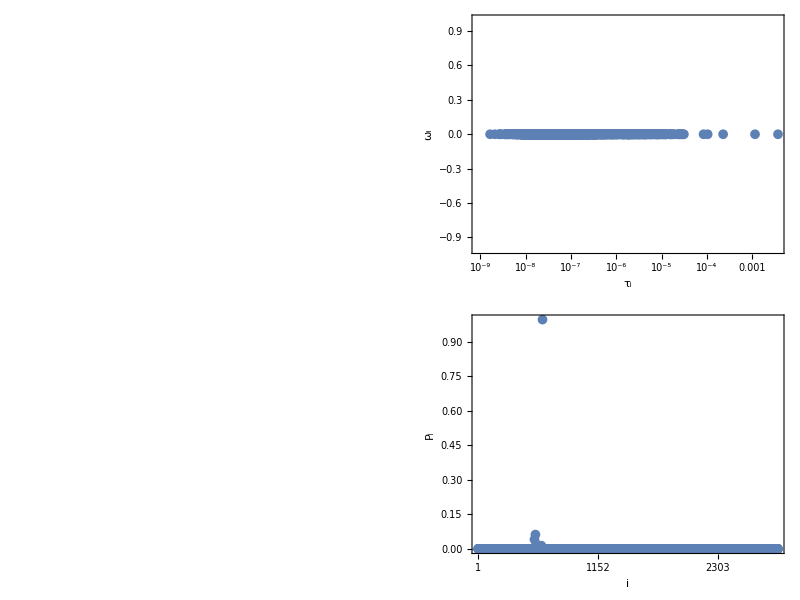

{100 (Ar_1)+O_1 H_1+10 (O_1 H_2),100 (Ar_1)+H_1+H_2+9 (O_1 H_2)+O_2,100 (Ar_1)+2 (H_2)+O_1 H_1+8 (O_1 H_2)+O_2,100 (Ar_1)+H_2+O_1+O_1 H_1+9 (O_1 H_2),100 (Ar_1)+H_1+2 (O_1 H_1)+9 (O_1 H_2)}

2414.73

2.31324

-1.65673×10^-9+0. ⅈ

0.699066

```mathematica
filebase="data/h2o2/5/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],dim];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,None},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Total[spforms*#]&/@multiindices[[Reverse[Ordering[Abs[evecs[[-1]]]]][[1;;5]]]]
Re[Total[temperatures*evecs[[-1]]]/Total[evecs[[-1]]]]
Re[Total[pressures*evecs[[-1]]]/Total[evecs[[-1]]]]
1/evals[[1]]
Total[Abs[evals]^2]/Total[Total[A^2]]
```

{12,4,9,13,60,556,564}

{H_2,H,O,O_2,OH,H_2O,HO_2,H_2O_2,0}

{OH+10 H_2+5 O_2,H+O+10 H_2+5 O_2,2 O+OH+10 H_2+4 O_2,2 H+OH+9 H_2+5 O_2,H+H_2O+9 H_2+5 O_2,O+10 H_2+HO_2+4 O_2,H+OH+9 H_2+HO_2+4 O_2}

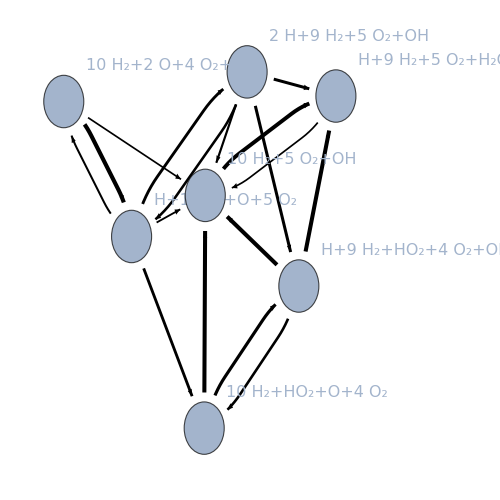

graph.pdf

```mathematica
indices=Join[{ind},First/@Position[Normal[A[[All,ind]]],u_/;u>0]]
spforms={Subscript["H", 2],"H","O",Subscript["O", 2],"OH","H_2O",Subscript["HO", 2],Subscript["H_2O", 2],0}
vertexlabels=Total[spforms*#]&/@multiindices[[indices]]
mat=Normal[A[[indices,indices]]]-DiagonalMatrix[Diagonal[Normal[A[[indices,indices]]]]]/.(u_/;u<1->0);p=GraphPlot[mat,VertexLabels->Table[i->Style[vertexlabels[[i]],16],{i,1,Length[indices]}],ImageSize->500,DataRange->{{-1,1},{-1,1}},VertexSize->0.5,DirectedEdges->True,EdgeShapeFunction->({Black, Opacity[1],AbsoluteThickness[0.2*Log[#2/.(DirectedEdge[a1_,a2_]:>mat[[a1,a2]])]],Arrowheads[0.003*Log[#2/.(DirectedEdge[a1_,a2_]:>mat[[a1,a2]])]],Arrow[#1, 0.2]} & )]
Export["graph.pdf",p]
```

12

0.+0. ⅈ

1.72686×10^-12

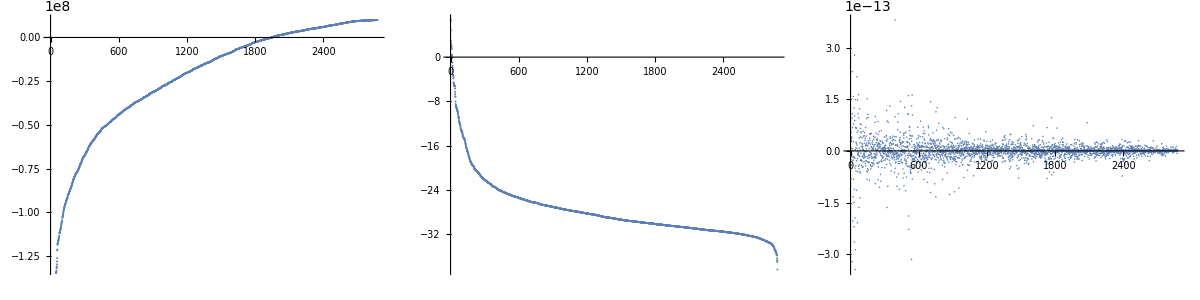

```mathematica
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
evals[[-1]]
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
Grid[{{ListPlot[Re[evals+1/(10^-7)],ImageSize->300],ListPlot[Log[Abs[#]]&/@Reverse[SortBy[α,Abs]],ImageSize->300,PlotRange->All],ListPlot[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]],PlotRange->All,ImageSize->300]}}]
```

1.15619+0. ⅈ

1.58811

1.75842

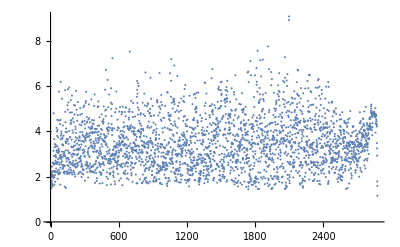

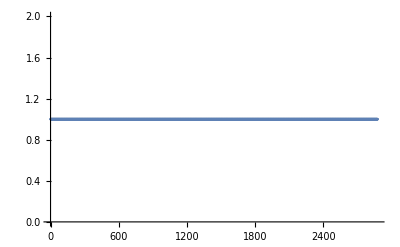

1.15619

9.06916

```mathematica
Total[evecs[[-1]]]
Total[Abs[evecs[[-2]]]]
Total[Abs[evecs[[1]]]]
ListPlot[Total/@Abs/@evecs]
ListPlot[Total/@(Abs[#]^2&/@evecs)]
Min[Total/@Abs/@evecs]
Max[Total/@Abs/@evecs]
```

12

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

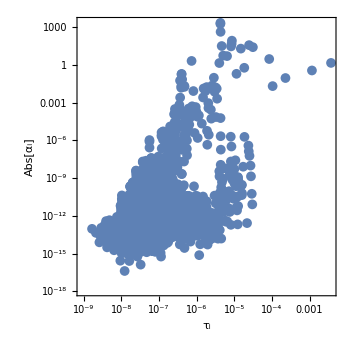
-Graphics- | -Graphics-

spectrum.pdf

```mathematica
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
evecs2=#/Total[Abs[#]]&/@evecs;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs2]];
evecs3=Reverse[SortBy[Transpose[{evecs2,Abs[α]}],#[[2]]&]][[All,1]];angles=(evecs3.ConjugateTranspose[evecs3])/Outer[Times,Norm/@evecs3,Norm/@evecs3];

p=Grid[{{ListLogLogPlot[Transpose[{-1/evals,Abs[α]}][[1;;-2]],PlotRange->All,Axes->False,Frame->True,FrameLabel->{Subscript[τ,i],Abs[Subscript["α",i]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->350,ImagePadding->{{95,25},{75,25}},PlotStyle->Directive[PointSize[0.02]]],Legended[rasterizeBackground[MatrixPlot[ArcCos[Abs[angles]],PlotRange->{0,Pi/2},ImageSize->350,FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16],FrameLabel->{i,j},FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},ImagePadding->{{95,25},{75,25}},ColorFunction->"TemperatureMap",PlotRange->{0,1}]],MatrixPlot[Table[i,{i,0,100},{j,0,100}],ColorFunction->"TemperatureMap",AspectRatio->10,ImageSize->{Automatic,200},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{None,Subscript[θ,ij]},{None,None}},FrameTicks->{{None,{{1,0},{26,DisplayForm[RowBox[{Pi,"/",8}]]},{51,DisplayForm[RowBox[{Pi,"/",4}]]},{76,DisplayForm[RowBox[{3Pi,"/",8}]]},{101,DisplayForm[RowBox[{Pi,"/",2}]]}}},{None,None}},DataReversed->True,LabelStyle->Directive[16,Black]]]}}]
Export["spectrum.pdf",p]
```

13

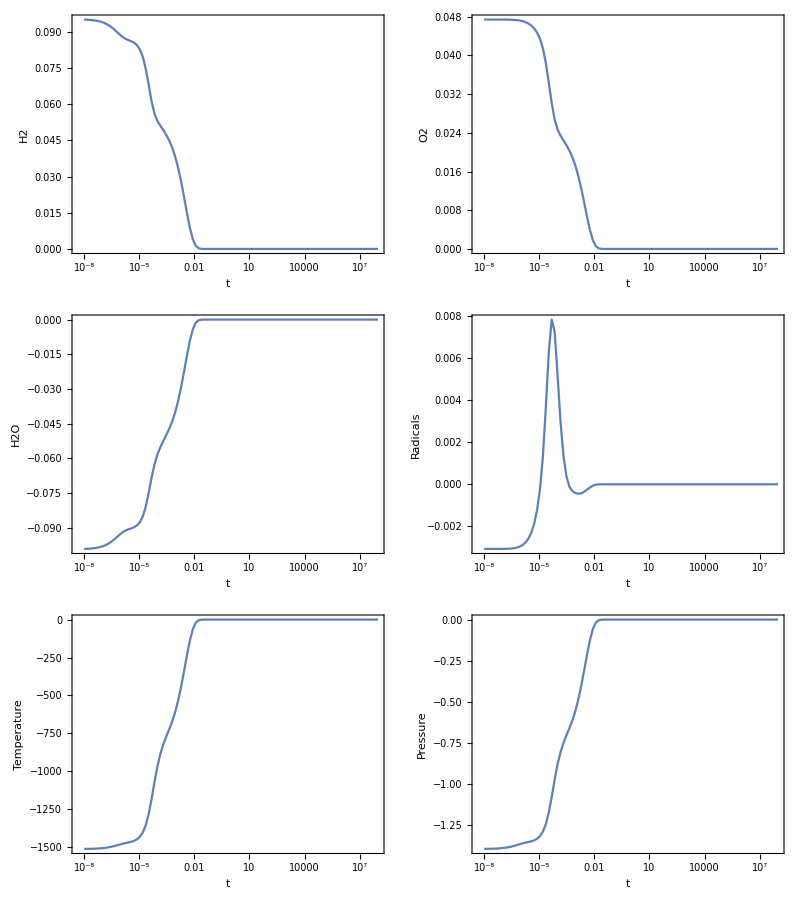

```mathematica
Nt=100;
t0=10.^-8;
t1=10^8.;
filebase="data/test";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];
h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
states=Table[pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{Length[evecs]}];If[Length[pos]==0,ConstantArray[0,dim],((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];
h2=Transpose[{times,Total/@(states.h2norm)}];
o2=Transpose[{times,Total/@(states.o2norm)}];
h2o=Transpose[{times,Total/@(states.h2onorm)}];
radicals=Transpose[{times,Total/@(states.radicalnorm)}];
temp=Transpose[{times,Total/@(states.temperaturenorm)}];
pres=Transpose[{times,Total/@(states.pressurenorm)}];
Grid[{{ListLogLinearPlot[h2,Axes->False,Frame->True,FrameLabel->{t,"H2"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True],ListLogLinearPlot[o2,Axes->False,Frame->True,FrameLabel->{t,"O2"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True]},{ListLogLinearPlot[h2o,Axes->False,Frame->True,FrameLabel->{t,"H2O"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True],ListLogLinearPlot[radicals,Axes->False,Frame->True,FrameLabel->{t,"Radicals"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True,PlotRange->All]},{ListLogLinearPlot[temp,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True],ListLogLinearPlot[pres,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True]}}]
```

```mathematica
evals[[-1]]=0;states=Table[pos=Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]];If[Length[pos]==0,ConstantArray[0,dim],((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];
radicals=Transpose[{times,Total/@(states.radicalnorm)}];
radicals[[1]]
```

{1.×10^-8,0.00840339+0. ⅈ}

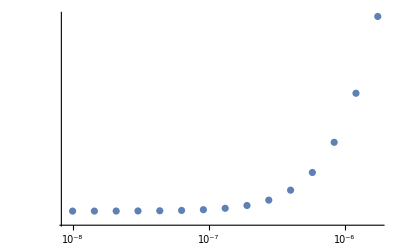

```mathematica
ListLogLogPlot[radicals[[1;;15]]]
```

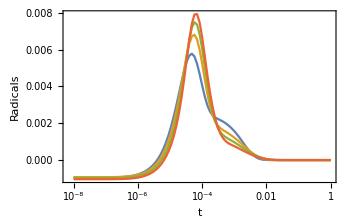

```mathematica
Nt=100;
t0=10.^-8;
t1=1.;
rads={};
Monitor[Do[
filebase="data/h2o2/"<>ToString[n]<>"/";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
states=Table[pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{Length[evecs]}];If[Length[pos]==0,ConstantArray[0,dim],((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];
radicals=Transpose[{times,Total/@(states.radicalnorm)}];
AppendTo[rads,radicals];,{n,3,6}],n]
ListLogLinearPlot[rads,Axes->False,Frame->True,FrameLabel->{t,"Radicals"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True,PlotRange->All]
```

data/h2o2/3/

{376,9,0.135705}

13

3.50888×10^-14

{3.37406,Null}

2.50556×10^8

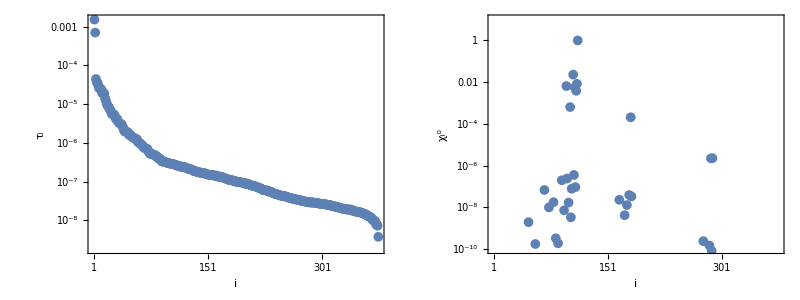

fig3.pdf

0.657416

```mathematica
filebase="data/h2o2/3/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
r=1/2;
AbsoluteTiming[angles=ParallelTable[ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}];]
max=Pi/2;
r=1;
cf=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*(Pi/2-#)/max]&;
max2=N[Max[A]]
cf2=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*#/max2]&;
p=Grid[{{Show[rasterizeBackground[MatrixPlot[Abs[A],ImageSize->350,AspectRatio->r,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[{Round[i],""},{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{None,None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},MaxPlotPoints->200]],Epilog->Inset[BarLegend[{cf2,{0,max2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->DisplayForm[RowBox[{Subsuperscript[W,i,k],"/",HoldForm[10^18]}]]],ImageScaled[{0.55,0.88}]]],Show[rasterizeBackground[MatrixPlot[angles,ImageSize->350,AspectRatio->r,PlotRange->All,FrameTicks->{Table[Round[i],{i,1,Length[evecs],(Length[evecs]-1)/5}],Table[{Round[i],""},{i,1,Length[evecs],(Length[evecs]-1)/5}]},FrameLabel->{{None,
None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},ColorFunctionScaling->False,ColorFunction->cf]],Epilog->Inset[BarLegend[{cf,{Pi/2-max,Pi/2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->Subsuperscript[θ,i,k]],ImageScaled[{0.55,0.88}]]]},{ListLogPlot[Reverse[-1/Re[evals[[1;;-2]]]],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript[τ,i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImagePadding->{{80,25},{65,10}},ImageSize->350,FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],ListLogPlot[Abs[evecs[[-1]]],PlotRange->{10^-10,10},Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subsuperscript[χ,i,0]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]]}}]
Export["fig3.pdf",p]
Total[Abs[evals]^2]/Total[svals^2]
```

data/h2o2/4/

{1141,9,0.833907}

7

Part::take: Cannot take positions 1141 through 1141 in {{-2.96213×10^-16+0. ⅈ,-1.53714×10^-15+0. ⅈ,-4.17755×10^-16+0. ⅈ,6.48312×10^-17+0. ⅈ,2.1274×10^-15+0. ⅈ,-2.4021×10^-17+0. ⅈ,2.19697×10^-7+0. ⅈ,«37»,-3.56254×10^-16+0. ⅈ,-0.00521046+0. ⅈ,-1.0278×10^-11+0. ⅈ,4.48108×10^-16+0. ⅈ,6.16866×10^-18+0. ⅈ,-6.83508×10^-13+0. ⅈ,«1091»},{«1»},«48»,«550»}.

Part::take: Cannot take positions 1140 through 1141 in {{-2.96213×10^-16+0. ⅈ,-1.53714×10^-15+0. ⅈ,-4.17755×10^-16+0. ⅈ,6.48312×10^-17+0. ⅈ,2.1274×10^-15+0. ⅈ,-2.4021×10^-17+0. ⅈ,2.19697×10^-7+0. ⅈ,«37»,-3.56254×10^-16+0. ⅈ,-0.00521046+0. ⅈ,-1.0278×10^-11+0. ⅈ,4.48108×10^-16+0. ⅈ,6.16866×10^-18+0. ⅈ,-6.83508×10^-13+0. ⅈ,«1091»},{«1»},«48»,«550»}.

Part::take: Cannot take positions 1139 through 1141 in {{-2.96213×10^-16+0. ⅈ,-1.53714×10^-15+0. ⅈ,-4.17755×10^-16+0. ⅈ,6.48312×10^-17+0. ⅈ,2.1274×10^-15+0. ⅈ,-2.4021×10^-17+0. ⅈ,2.19697×10^-7+0. ⅈ,«37»,-3.56254×10^-16+0. ⅈ,-0.00521046+0. ⅈ,-1.0278×10^-11+0. ⅈ,4.48108×10^-16+0. ⅈ,6.16866×10^-18+0. ⅈ,-6.83508×10^-13+0. ⅈ,«1091»},{«1»},«48»,«550»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

ListLogPlot::lpn: norms is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

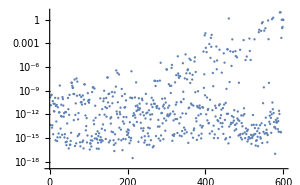
-Graphics- | ListLogPlot[norms,ImageSize→300]

```mathematica
filebase="data/h2o2/4/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Monitor[norms=Table[vecs=evecs[[dim-n;;dim]];αn=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[vecs];{n,Norm[Normal[SparseArray[{{ind}->1},{dim}]]-αn.vecs]},{n,0,dim-1,1}];,N[n/dim]]
Grid[{{ListLogPlot[Abs[α],PlotRange->All,ImageSize->300],ListLogPlot[norms,ImageSize->300]}}]
```

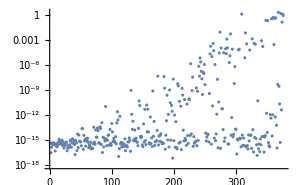

```mathematica
n=dim-1;
vecs=evecs[[dim-n;;dim]];αn=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[vecs];
ListLogPlot[Abs[αn],PlotRange->All,ImageSize->300]
```

### Non - normality measure

```mathematica
filebase="data/test"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evals[[-1]]=0;
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0,u[[8]]==0]
{pressures[[ind]],temperatures[[ind]],multiindices[[ind]]}
```

data/test

{842,9,0.117911}

50

{1.,1000.,{6,0,0,3,1,0,0,0,60}}

data/test

{842,9,0.117911}

{1.,1000.,{6,0,0,3,1,0,0,0,60}}

{0.391909,Null}

{0.551292,Null}

{0.351183,Null}

{0.233841,Null}

{0.127109,Null}

{0.113206,Null}

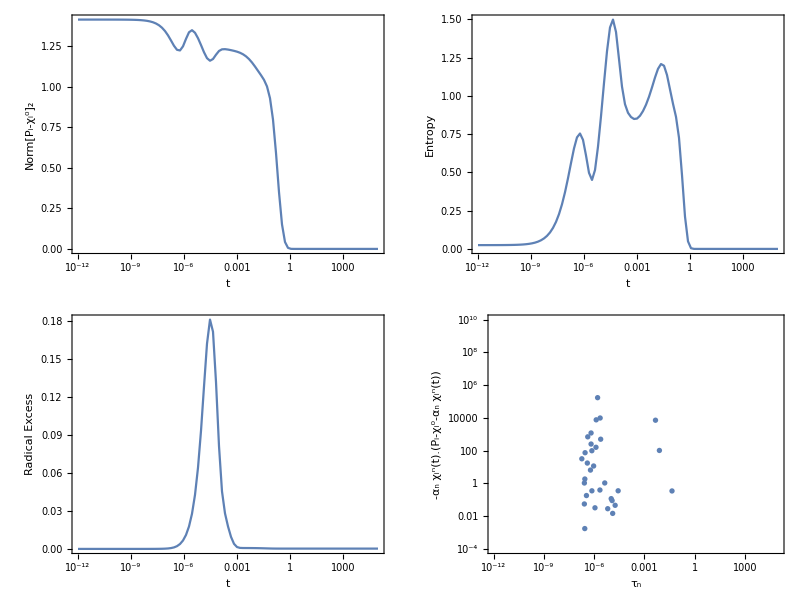

explosive.pdf

```mathematica
filebase="data/test"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evals[[-1]]=0;
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0,u[[8]]==0];
{pressures[[ind]],temperatures[[ind]],multiindices[[ind]]}
AbsoluteTiming[α=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs];]
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]]))&/@multiindices)];

Nt=100;
t0=10.^-12;
t1=10^5.;
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
AbsoluteTiming[states=Table[pos=Intersection[First/@Position[α,u_/;Abs[u]>10^-3],First/@Position[evals,u_/;Abs[u*t]<100]];Re[((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];]
AbsoluteTiming[projections=Table[t=-1/Re[evals[[i]]];pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{dim,i}];If[pos=={},10^-16,-Re[Conjugate[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])].((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])/Norm[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])]^2]-1],{i,Cases[Range[Length[evals]-1],u_/;Abs[α][[u]]>10^-6]}];]
tau=-1/Re[evals[[Cases[Range[Length[evals]-1],u_/;Abs[α][[u]]>10^-6]]]];
AbsoluteTiming[Pnorm=Norm[#-α[[-1]]*evecs[[-1]],2]&/@states;]
AbsoluteTiming[entropy=Total/@(-Abs[(#-α[[-1]]*evecs[[-1]])]*Log[10^-16+Abs[(#-α[[-1]]*evecs[[-1]])]]&/@states);]
AbsoluteTiming[radicals=Total/@((Re[#-α[[-1]]*evecs[[-1]]]&/@states).radicalnorm);]
file=OpenWrite[filebase<>"times.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[times],"Real64"];
Close[file];
file=OpenWrite[filebase<>"states.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[states],"Real64"];
Close[file];
file=OpenWrite[filebase<>"projections.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[projections],"Real64"];
Close[file];
file=OpenWrite[filebase<>"norms.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[Pnorm],"Real64"];
Close[file];
file=OpenWrite[filebase<>"entropies.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[entropy],"Real64"];
Close[file];
file=OpenWrite[filebase<>"radicals.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[radicals],"Real64"];
Close[file];
file=OpenWrite[filebase<>"taus.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[tau],"Real64"];
Close[file];
p=Grid[{{ListLogLinearPlot[Transpose[{times,Pnorm}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t",Subscript[Norm[Subscript[P,i]-Subsuperscript[χ,i,0]],2]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLinearPlot[Transpose[{times,entropy}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Entropy"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300]},{ListLogLinearPlot[Transpose[{times,radicals}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Radical Excess"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLogPlot[Transpose[{tau,projections}],Axes->False,Frame->True,FrameLabel->{Subscript[τ,n],HoldForm[-Subscript["α",n]*Subsuperscript[χ,i,n]["t"].(Subscript[P,i]-Subsuperscript[χ,i,0]-Subscript["α",n]*Subsuperscript[χ,i,n]["t"])]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},{10^-4,10^10}},ImageSize->300]}}]
Export["explosive.pdf",p]
```

{0.427212,Null}

{2.34266,Null}

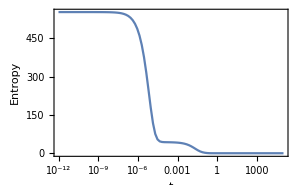

1.00006+0. ⅈ

```mathematica
AbsoluteTiming[U=PseudoInverse[#/Norm[#,1]&/@evecs];]
AbsoluteTiming[entropy=(#.U.ConjugateTranspose[U].#)&/@states;]
ListLogLinearPlot[Transpose[{times,entropy}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Entropy"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300]
entropy[[-1]]
```

```mathematica
Monitor[Do[filebase="data/sweep/"<>ToString[n]<>"_"<>ToString[m];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evals[[-1]]=0;
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
α=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
Nt=100;
t0=10.^-10;
t1=10^5;
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
states=Table[pos=Intersection[First/@Position[α,u_/;Abs[u]>10^-3],First/@Position[evals,u_/;Abs[u*t]<100]];Re[((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];
projections=Table[t=-1/Re[evals[[i]]];pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{dim,i}];If[pos=={},10^-16,-Re[Conjugate[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])].((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])/Norm[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])]^2]],{i,Cases[Range[dim-1],u_/;Abs[α][[u]]>10^-6]}];
tau=-1/Re[evals[[Cases[Range[dim-1],u_/;Abs[α][[u]]>10^-6]]]];
Pnorm=Norm[#-α[[-1]]*evecs[[-1]],2]&/@states;
entropy=Total/@(-Abs[(#-α[[-1]]*evecs[[-1]])]*Log[10^-16+Abs[(#-α[[-1]]*evecs[[-1]])]]&/@states);
radicals=Total/@((Re[#-α[[-1]]*evecs[[-1]]]&/@states).radicalnorm);
file=OpenWrite[filebase<>"times.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[times],"Real64"];
Close[file];
file=OpenWrite[filebase<>"states.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[states],"Real64"];
Close[file];
file=OpenWrite[filebase<>"projections.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[projections],"Real64"];
Close[file];
file=OpenWrite[filebase<>"norms.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[Pnorm],"Real64"];
Close[file];
file=OpenWrite[filebase<>"entropies.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[entropy],"Real64"];
Close[file];
file=OpenWrite[filebase<>"radicals.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[radicals],"Real64"];
Close[file];
file=OpenWrite[filebase<>"taus.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[tau],"Real64"];
Close[file];,{n,0,50},{m,0,50}];,{m,n}]
```

```mathematica
Monitor[sweep=Table[filebase="data/sweep/"<>ToString[n]<>"_"<>ToString[m];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];times=BinaryReadList[filebase<>"times.dat", "Real64"];states=BinaryReadList[filebase<>"states.dat", "Real64"];projections=BinaryReadList[filebase<>"projections.dat", "Real64"];Pnorm=BinaryReadList[filebase<>"norms.dat", "Real64"];entropy=BinaryReadList[filebase<>"entropies.dat", "Real64"];
radicals=BinaryReadList[filebase<>"radicals.dat", "Real64"];tau=BinaryReadList[filebase<>"taus.dat", "Real64"];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
{temperatures[[ind]],pressures[[ind]], times,Pnorm,entropy,radicals,tau,projections},{m,0,50},{n,0,50}];,{m,n}]
```

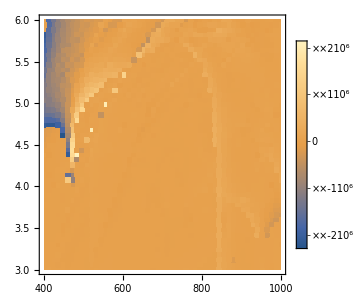
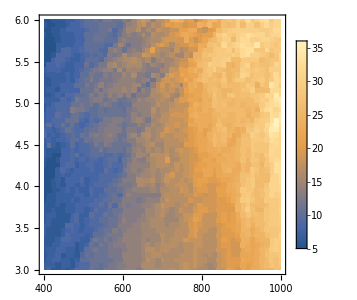
-Graphics- | -Graphics-

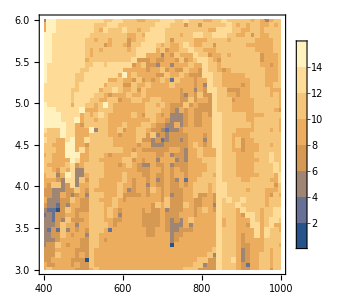
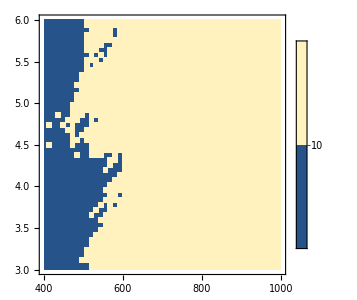
-Graphics- | -Graphics-

```mathematica
Grid[{{ListDensityPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Total[#[[8]]]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300],
ListDensityPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Count[#[[8]],u_/;u>0]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300]}}]
Grid[{{ListContourPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Log[Abs[Total[#[[8]]]]]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300],
ListContourPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Count[#[[8]],u_/;u>0]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300,Contours->{10}]}}]
```

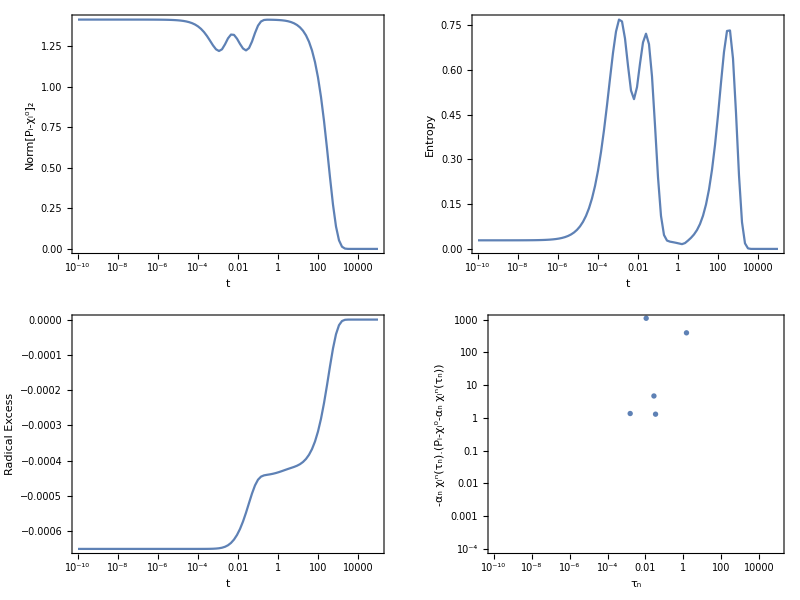

```mathematica
n=1;
m=1;
Grid[{{ListLogLinearPlot[Transpose[{sweep[[n,m,3]],sweep[[n,m,4]]}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t",Subscript[Norm[Subscript[P,i]-Subsuperscript[χ,i,0]],2]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLinearPlot[Transpose[{sweep[[n,m,3]],sweep[[n,m,5]]}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Entropy"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300]},{ListLogLinearPlot[Transpose[{sweep[[n,m,3]],sweep[[n,m,6]]}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Radical Excess"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLogPlot[Transpose[{sweep[[n,m,7]],sweep[[n,m,8]]}],Axes->False,Frame->True,FrameLabel->{Subscript[τ,"n"],HoldForm[-Subscript["α","n"]*Subsuperscript[χ,i,"n"][Subscript[τ,"n"]].(Subscript[P,i]-Subsuperscript[χ,i,0]-Subscript["α","n"]*Subsuperscript[χ,i,"n"][Subscript[τ,"n"]])]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},{10^-4,1000}},ImageSize->300]}}]
```

## Concentration evolutions

```mathematica
times
```

$Failed⟦17;;-1⟧

data/h2o2/

Table::iterb: Iterator {t,times} does not have appropriate bounds.

{41.8628,Null}

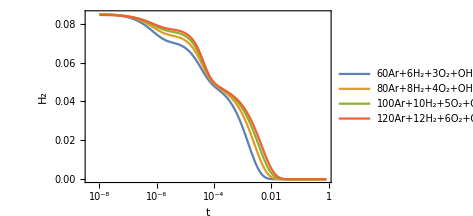
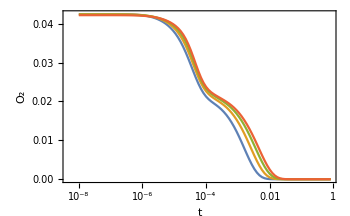
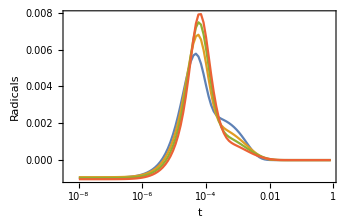
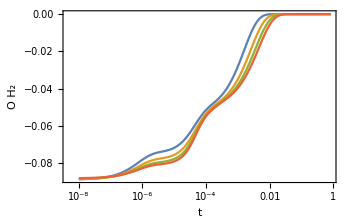
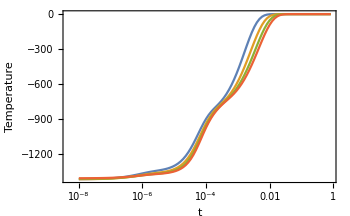
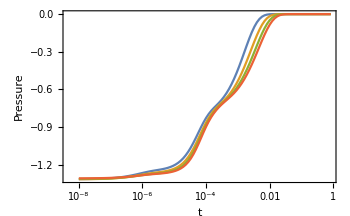

```mathematica
o2dats={};
h2dats={};
h2odats={};
radicaldats={};
temperaturedats={};
pressuredats={};
initials={};
filebase0="data/h2o2/"
AbsoluteTiming[Monitor[Do[filebase=filebase0<>ToString[m]<>"/";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
elements=dat[[3]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
states=Table[pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{Length[evecs]}];If[Length[pos]==0,ConstantArray[0,dim],((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];
initial=Total[DeleteCases[If[#[[1]]>0, If[#[[1]]==1,DisplayForm[RowBox[{ToString[#[[2]]]}]], DisplayForm[RowBox[{#[[1]],#[[2]]}]]]]&/@Transpose[Table[{multiindices[[i]],spforms},{i,1,dim}][[ind]]],Null]];
AppendTo[initials,initial];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
(*Abs[(Total[#]-Total[evecs[[-1]].h2norm]/Total[evecs[[-1]]])]*)
AppendTo[h2dats,Transpose[{times,Total[#]&/@(states.h2norm)}]];
AppendTo[o2dats,Transpose[{times,Total[#]&/@(states.o2norm)}]];
AppendTo[radicaldats,Transpose[{times,Total[#]&/@(states.radicalnorm)}]];
AppendTo[h2odats,Transpose[{times,Total[#]&/@(states.h2onorm)}]];
AppendTo[temperaturedats,Transpose[{times,Total[#]&/@(states.temperaturenorm)}]];
AppendTo[pressuredats,Transpose[{times,Total[#]&/@(states.pressurenorm)}]];
p=Legended[ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]];,{m,3,6}],{m,n, p}]]
p=Legended[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}},Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]]
```

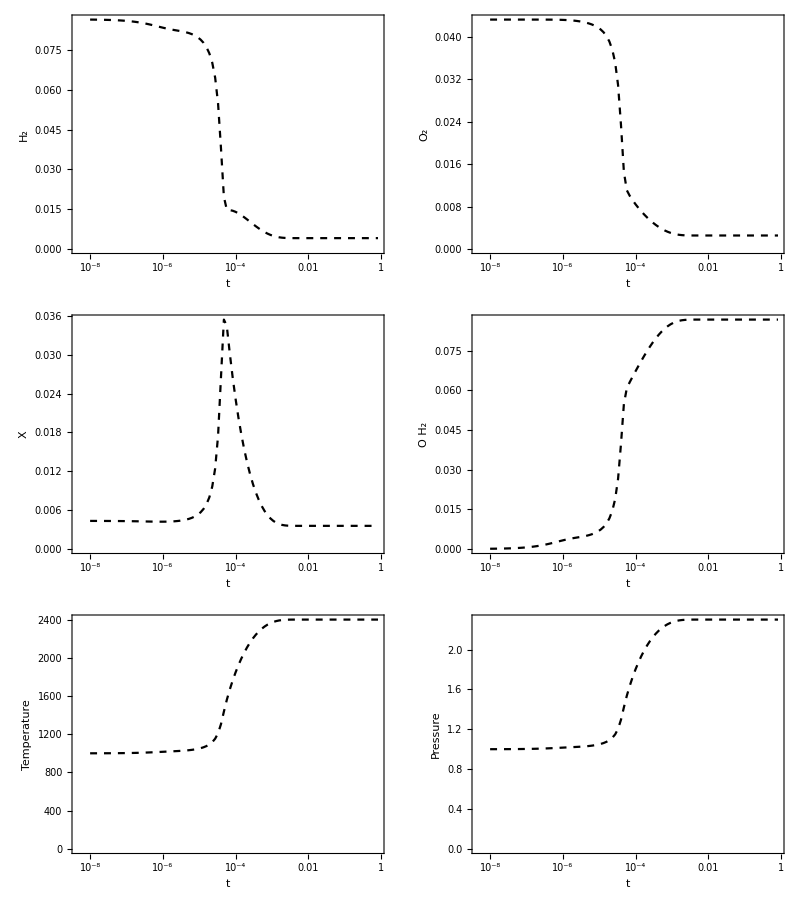

```mathematica
filebase="data/h2o2/h2o2";
filebase="data/ctest";
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],9]];
{{p0,p1},{p2,p3},{p4,p5}}={{ListLogLinearPlot[Transpose[{times,concentrations[[1]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{times,concentrations[[4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{times,concentrations[[2]]+concentrations[[3]]+concentrations[[5]]+concentrations[[7]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{times,concentrations[[6]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{times,temperatures}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{times,pressures}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]}};
Grid[{{p0,p1},{p2,p3},{p4,p5}}]
```

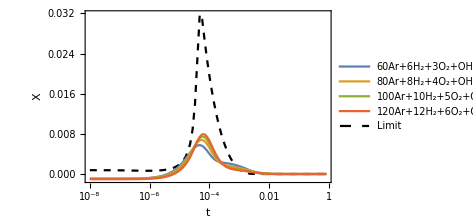

```mathematica
radicalconcentration=concentrations[[2]]+concentrations[[3]]+concentrations[[5]]+concentrations[[7]];p2=ListLogLinearPlot[Transpose[{times,radicalconcentration-radicalconcentration[[-1]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]];
p=Legended[Show[p2,ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],PlotRange->All],Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{"Limit"}]],Right]]
```

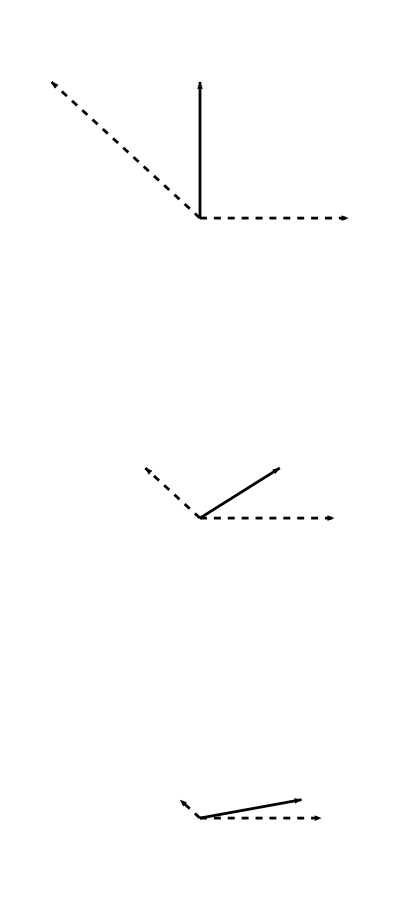

```mathematica
ϵ=0.25;
x1[t_]:=Exp[-t]*{1,0}
x2[t_]:=Exp[-10*t]*{-1,ϵ}
x[t_]:=x1[t]+x2[t]
p0=Grid@Transpose[{Table[Graphics[{AbsoluteThickness[2],Arrowheads[0.07],Arrow[{{0,0},x[t]}],Dashed, Arrow[{{0,0},x1[t]}],Arrow[{{0,0},x2[t]}]},PlotRange->{{-1.1,1.1},{-0.1,ϵ+0.1}},ImageSize->250],{t,0,0.2,0.1}]}]
```

data/h2o2/3/

{18,376,1.3744,12639,10}

4.46967×10^-15

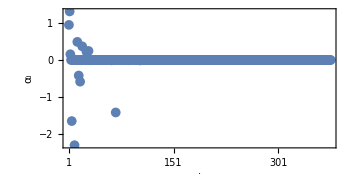
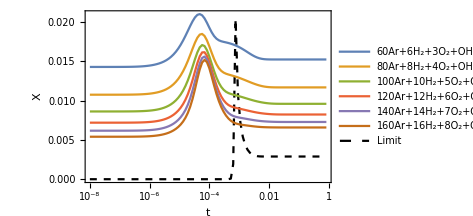
-Graphics- | -Graphics-
-Graphics-

fig2.pdf

```mathematica
filebase="data/h2o2/3/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
p=Grid[{{Grid[{{ListPlot[Reverse[α],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript["α",i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],p0}}]},{p}}]
Export["fig2.pdf",p]
```

## Runtimes

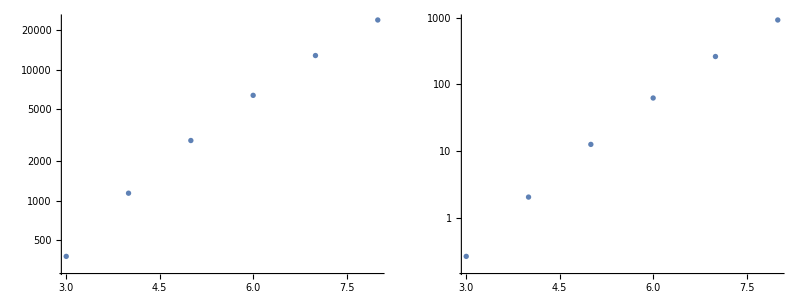

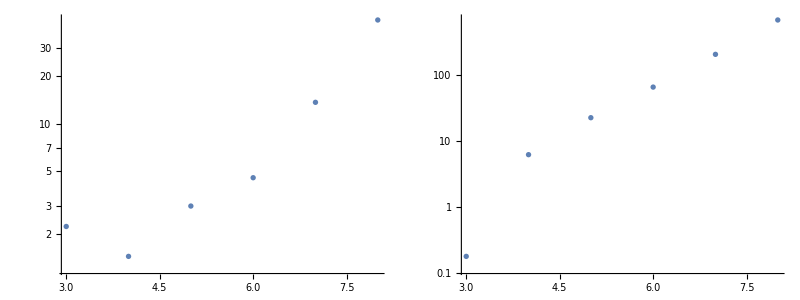

```mathematica
Grid[{{ListLogPlot[Import["statesruntime.dat"][[All,{1,2}]],ImageSize->300],ListLogPlot[Import["statesruntime.dat"][[All,{1,3}]],ImageSize->300]}}]
Grid[{{ListLogPlot[Import["calculateruntime.dat"][[All,{1,2}]],ImageSize->300],ListLogPlot[Import["eigenvaluesruntime.dat"][[All,{1,2}]],ImageSize->300]}}]
```

```mathematica
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["statesruntime.dat"][[All,{1,3}]][[2;;-1]],{1,x},x]
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["calculateruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["eigenvaluesruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]

Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["statesruntime.dat"][[All,{1,3}]][[2;;-1]],{1,x},x]*1/3600/.x->10
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["calculateruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]*1/3600/.x->10
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["eigenvaluesruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]*1/3600/.x->12
```

0.00563486 4.58589^x

0.0422938 2.31821^x

0.0628461 3.18854^x

6.43894

0.0526626

19.2788

## Kmatrix

data/grimech

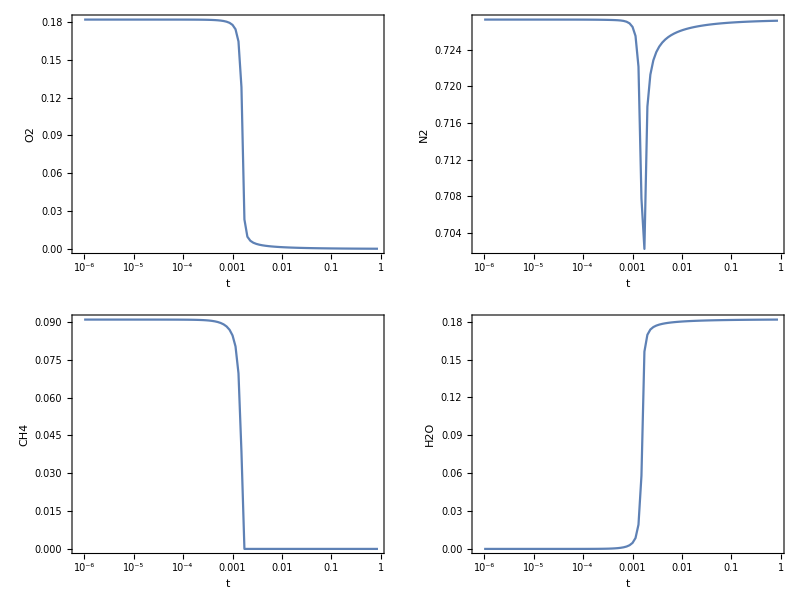

```mathematica
filebase="data/grimech"
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
Nt=Length[times];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],Length[times]];
ns=Length[evals];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],ns]];
Grid[{{ListLogLinearPlot[Transpose[{times,concentrations[[4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"O2"}],
ListLogLinearPlot[Transpose[{times,concentrations[[48]]}],PlotRange->All,Joined->True, Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"N2"}]},
{ListLogLinearPlot[Transpose[{times,concentrations[[14]]}],PlotRange->All,Joined->True, Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"CH4"}],
ListLogLinearPlot[Transpose[{times,concentrations[[6]]}],PlotRange->All,Joined->True, Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"H2O"}]}}]
```

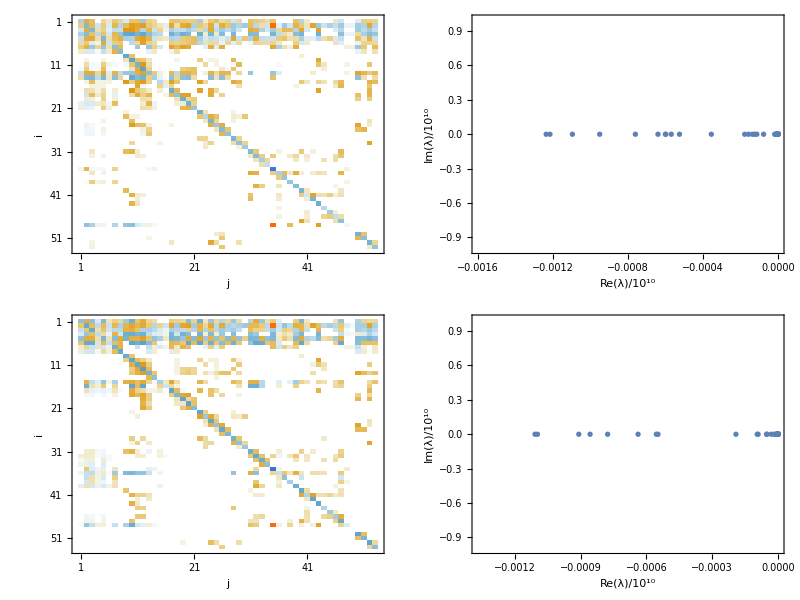

```mathematica
matrices=Partition[Partition[BinaryReadList[filebase<>"matrices.npy","Real64"][[17;;-1]],ns],ns];
p=Grid[{{MatrixPlot[matrices[[1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices[[1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]},{MatrixPlot[matrices[[-1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices[[-1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]}}]
```

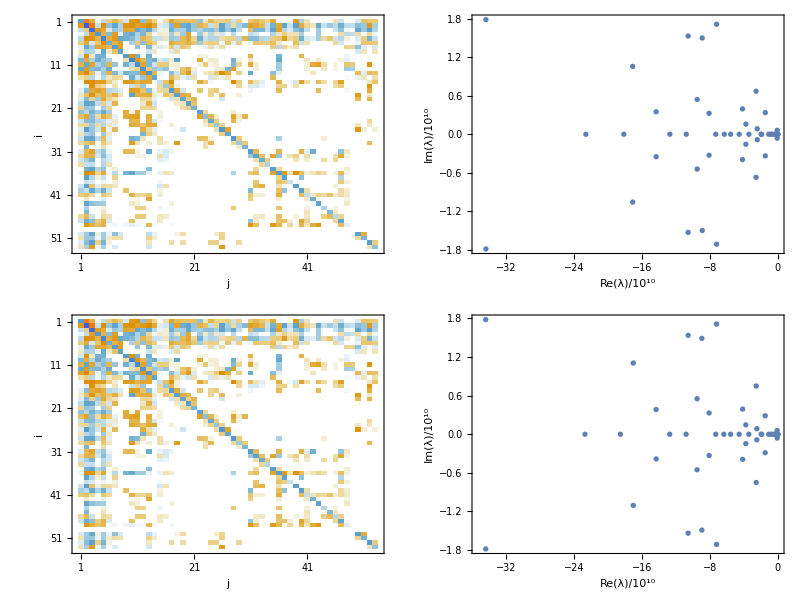

```mathematica
matrices2=Partition[Partition[BinaryReadList[filebase<>"matrices2.npy","Real64"][[17;;-1]],ns],ns];
p=Grid[{{MatrixPlot[matrices2[[1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices2[[1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]},{MatrixPlot[matrices2[[-1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices2[[-1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]}}]
```